```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,20000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Tally[{imp9,imp3,imp5,imp1,imp,imp,imp14,imp13,imp1,imp4,imp7,imp,imp,imp10,imp2,imp12,imp6,imp,imp13,imp4,imp6,imp,imp11,imp1,imp,imp5,imp,imp10,imp2,imp,imp14,imp,imp9,imp12,imp6,imp11,imp,imp,imp3,imp,imp10,imp3,imp8,imp9,imp14,imp12,imp,imp8,imp7,imp}]
```

{{imp9,3},{imp3,3},{imp5,2},{imp1,3},{imp,15},{imp14,3},{imp13,2},{imp4,2},{imp7,2},{imp10,3},{imp2,2},{imp12,3},{imp6,3},{imp11,2},{imp8,2}}

```mathematica
misfit50[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp5,imp,imp9,imp5,imp1,imp6,imp13,imp,imp,imp,imp,imp3,imp,imp13,imp12,imp11,imp2,imp,imp7,imp9,imp,imp,imp4,imp,imp,imp12,imp,imp14,imp8,imp11,imp8,imp,imp2,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
Table[{ω,tra},{ω,Range[0,4,0.01]}]
]
```

```mathematica
data=Table[misfit50[0.5,0,1.48],100]
```

{{{0.,2.8×10^-7},{0.01,2.78265×10^-7},{0.02,2.79446×10^-7},{0.03,1.86481×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,1.13005×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.7123×10^-7},{0.11,4.18578×10^-7},378,{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.59151×10^-9}},98,{1}}
 |  |  |  |

```mathematica
υ50[n_,x_,y_]:=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}]
```

```mathematica
aa50=Table[υ50[n,1.48,0],{n,Range[1,100,1]}]
```

{{0.00472509,0.00202093,0.00130966,0.00124737,0.00158968,0.00220597,0.00252977},{0.00383273,0.0014621,0.000907885,0.00104867,0.00152348,0.00225348,0.00269728},{0.00434892,0.00173992,0.00112579,0.00117506,0.00162828,0.00212399,0.0026739},{0.00426173,0.00188424,0.00129571,0.00145163,0.00191754,0.0024914,0.0029263},{0.00356392,0.00143705,0.00107633,0.00142926,0.00184054,0.00258257,0.00305333},{0.00299575,0.000972159,0.00077154,0.00107171,0.00171023,0.00242361,0.00300819},{0.00358799,0.00117147,0.00070646,0.00090421,0.00142047,0.0020541,0.0026041},{0.0040684,0.00174713,0.00118281,0.00134333,0.00181195,0.00243419,0.00290965},{0.0045729,0.00184349,0.00106116,0.00108474,0.00139381,0.00197689,0.00240247},{0.00321917,0.00108106,0.000665663,0.000925312,0.00157938,0.00230795,0.00279966},{0.00384827,0.00151631,0.00103479,0.00111847,0.00159617,0.00215464,0.00265354},{0.00346114,0.00127057,0.000851275,0.00106692,0.00165768,0.00232628,0.00289786},{0.00341764,0.00124333,0.000756158,0.00105801,0.00170209,0.00244264,0.00295777},{0.00289909,0.00102072,0.000751133,0.00124515,0.00186384,0.00274263,0.00325889},{0.00498225,0.00225843,0.00147466,0.00139296,0.00170093,0.00222283,0.00252832},{0.00407423,0.00156966,0.000948689,0.00110668,0.00159457,0.00218198,0.00267051},{0.00379116,0.00138007,0.00071928,0.000809685,0.00121082,0.00183277,0.00227154},{0.00307805,0.00112949,0.000796114,0.001107,0.00163859,0.00231908,0.00286513},{0.00368213,0.00140389,0.000961012,0.00111828,0.00168661,0.00248024,0.00281496},{0.00532927,0.00248497,0.00157628,0.00147218,0.00170319,0.00210796,0.00245468},{0.00284457,0.000969895,0.000740026,0.00109512,0.0017962,0.00264316,0.00320378},{0.00400689,0.00168029,0.00115704,0.00134269,0.0017961,0.00250358,0.00297811},{0.00401614,0.00155935,0.000967239,0.0010198,0.00152826,0.00214739,0.00257189},{0.00407364,0.00167255,0.00108474,0.0011725,0.00167978,0.0022999,0.00276493},{0.00259824,0.000831996,0.000753922,0.00128761,0.0021224,0.00307439,0.00366608},{0.00399739,0.00149035,0.000861117,0.00102298,0.00156958,0.00214327,0.00259653},{0.00294182,0.00103889,0.000838755,0.00123751,0.00189318,0.00267608,0.00325667},{0.00321759,0.00117209,0.000880772,0.00120006,0.00184588,0.00262467,0.00310841},{0.00382562,0.00146369,0.000928478,0.00110615,0.00159679,0.00226543,0.00267217},{0.00354248,0.00120359,0.000715328,0.0009346,0.00147113,0.00217997,0.00269146},{0.00349042,0.00141107,0.00106933,0.00122796,0.00175643,0.00250568,0.00301006},{0.00358952,0.00127014,0.000733478,0.00091661,0.00140002,0.00217049,0.00261521},{0.0040949,0.00166365,0.00111313,0.00118181,0.00167154,0.00229231,0.0027603},{0.00447972,0.00190898,0.00112224,0.00124202,0.00147542,0.00203273,0.00243449},{0.00316519,0.0013032,0.0010676,0.00147134,0.00218741,0.00303755,0.00358887},{0.00313143,0.00121717,0.000965215,0.00133364,0.0019988,0.0027769,0.00341007},{0.00515808,0.00229052,0.00137329,0.00124697,0.0015641,0.0019581,0.00235595},{0.0028551,0.00100042,0.000799106,0.0012405,0.00198067,0.00284322,0.00339116},{0.0031245,0.00116531,0.000914247,0.00124734,0.00184974,0.00256336,0.00312476},{0.0041447,0.0018507,0.00141192,0.00166989,0.00206963,0.00286118,0.00328817},{0.00324427,0.00126903,0.000869052,0.0012324,0.00175492,0.00249534,0.00297403},{0.00399497,0.00148432,0.000916771,0.000983515,0.00158471,0.00219912,0.00269192},{0.00368897,0.0013355,0.000820576,0.00103863,0.00155705,0.00228774,0.0027877},{0.00388283,0.00146678,0.000893962,0.00103374,0.00162494,0.00230908,0.00271619},{0.00400516,0.00134833,0.000653436,0.000679138,0.00107283,0.00166631,0.00203926},{0.00405784,0.00159664,0.00103599,0.00117272,0.00185901,0.00255298,0.00306958},{0.00286631,0.000968715,0.000737954,0.0011267,0.00178936,0.00255328,0.00312945},{0.00312935,0.00116392,0.000852781,0.00120226,0.00183073,0.00264311,0.0031654},{0.00260177,0.000807407,0.000678247,0.00114352,0.00184267,0.00273833,0.00328726},{0.00406884,0.00180645,0.00118908,0.00137175,0.00175756,0.00233073,0.0028181},{0.00272058,0.00102117,0.000963065,0.00149141,0.00240753,0.00330512,0.00389914},{0.00287348,0.000983354,0.0008026,0.00119856,0.00198368,0.00284212,0.00339522},{0.00262892,0.000845322,0.000702889,0.00120252,0.00194995,0.00284023,0.00342207},{0.00360029,0.00141675,0.00100976,0.00126137,0.00188916,0.00257177,0.00311398},{0.00389774,0.00142895,0.000796578,0.000850531,0.00128652,0.00188009,0.00232633},{0.00355324,0.00144189,0.00101729,0.00135553,0.00197347,0.00272661,0.00329081},{0.00369355,0.00143035,0.000944641,0.00117061,0.00174392,0.00243309,0.00292161},{0.00308857,0.00108545,0.000872195,0.00130475,0.00205663,0.00278507,0.0033656},{0.00285261,0.000987599,0.000771396,0.00119675,0.00187242,0.00264616,0.00326013},{0.00434687,0.00171118,0.00102253,0.00107647,0.00149632,0.00208872,0.00255338},{0.00381811,0.00156658,0.00112536,0.00140417,0.00190149,0.00256929,0.00311668},{0.00307604,0.00105791,0.000747318,0.00111078,0.00184418,0.00267805,0.00317682},{0.00380009,0.00140693,0.00079575,0.000910713,0.00136544,0.00204262,0.0024495},{0.00378547,0.00132816,0.000768731,0.000891504,0.00148163,0.00218656,0.0026108},{0.00326785,0.00133512,0.00107665,0.00153618,0.00214001,0.00298224,0.00357414},{0.00367947,0.00144307,0.000945682,0.00119896,0.00168099,0.0023397,0.00288016},{0.00434426,0.00179905,0.00101636,0.00114077,0.00150762,0.00211598,0.00249087},{0.00337433,0.00125329,0.000879731,0.00117741,0.00168041,0.00245895,0.0028852},{0.00397843,0.00156092,0.00105771,0.00123143,0.00180438,0.00256936,0.00299037},{0.00347106,0.00125273,0.000861064,0.00114991,0.0016059,0.00237396,0.00284841},{0.00365897,0.00149624,0.00109741,0.00128163,0.00182702,0.00250431,0.00297302},{0.00402271,0.00163994,0.00106601,0.00114947,0.00159245,0.00228817,0.00268924},{0.00314858,0.00119069,0.000913499,0.00125289,0.00186644,0.00267993,0.00321846},{0.00340654,0.00126879,0.000877927,0.00110654,0.00174364,0.00243065,0.002898},{0.0042141,0.00184311,0.00123384,0.0014015,0.00173279,0.00232224,0.00287642},{0.00370161,0.00159657,0.00114636,0.00137781,0.0018723,0.00239933,0.00295786},{0.00430524,0.00184338,0.00121312,0.00130784,0.00177723,0.00236891,0.0029238},{0.00388207,0.00146174,0.000875623,0.00102108,0.00150016,0.00209311,0.00259628},{0.00334826,0.00139626,0.00109451,0.00151646,0.0020353,0.00284855,0.00340515},{0.00254625,0.000962926,0.000972449,0.00147897,0.00228261,0.00324784,0.00382192},{0.00291243,0.00104692,0.000825856,0.00123132,0.00192435,0.00274724,0.00333099},{0.00427808,0.00175012,0.0010601,0.0011292,0.00158015,0.00207138,0.00250939},{0.00399116,0.00159383,0.000954109,0.00111804,0.00155474,0.00215264,0.00261311},{0.00371093,0.00143064,0.000990587,0.00125202,0.00168191,0.00238674,0.00288338},{0.00301333,0.0011315,0.000909003,0.00129693,0.00205,0.0028557,0.00340142},{0.00381318,0.00157006,0.0010412,0.00120627,0.00180866,0.0024023,0.00287815},{0.00402907,0.00148319,0.000832017,0.000950758,0.00144211,0.00201932,0.00249349},{0.00347842,0.00130187,0.000877998,0.0012021,0.00189003,0.00264059,0.00318023},{0.0032061,0.00115804,0.000890071,0.00119994,0.00188796,0.00268358,0.00326335},{0.00325159,0.00127993,0.00100802,0.00134589,0.00207258,0.0028972,0.00344721},{0.0045583,0.00198088,0.00129507,0.00135481,0.00166691,0.00220208,0.00255814},{0.00416653,0.00165495,0.00104882,0.00106613,0.00144168,0.00204008,0.00244376},{0.00351359,0.00126305,0.000820388,0.00113737,0.0016556,0.00243023,0.00285407},{0.00212156,0.0009151,0.00117823,0.0019424,0.00301142,0.00407901,0.00472656},{0.003564,0.00127499,0.0008389,0.00105333,0.0016246,0.00233241,0.00283471},{0.00422964,0.00182307,0.00123152,0.00141329,0.00169655,0.00227906,0.00270916},{0.00346563,0.00139814,0.00100432,0.00129846,0.00200737,0.00272801,0.00326575},{0.00379141,0.00140327,0.000960286,0.00112636,0.00168485,0.00236676,0.00291339},{0.00318884,0.00109052,0.000809178,0.00110682,0.00185427,0.00263963,0.00313107},{0.0031001,0.00109653,0.000749785,0.00112189,0.00169592,0.00250163,0.00300811}}

```mathematica
ζ50=Mean[Table[Abs[3-Position[aa50[[x]],Min[aa50[[x]]]][[1,1]]]/3,{x,100}]]
```

1/50

```mathematica
misfit100[n_,x_,y_]:=Module[{},υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m100.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
aa100=Table[misfit100[n,0,1.48],{n,100}]
ζ100=Mean[Table[Abs[3-Position[aa100[[x]],Min[aa100[[x]]]][[1,1]]]/3,{x,100}]]
```

{{0.00472953,0.00196495,0.00127232,0.00125185,0.00163301,0.00216997,0.00263705},{0.00385976,0.00138316,0.000880618,0.00109907,0.00156282,0.00220862,0.00274784},{0.00435806,0.00175884,0.00108695,0.00120059,0.00157989,0.00215502,0.0026848},{0.0042699,0.00185134,0.00132925,0.00145164,0.00184948,0.00248514,0.0029972},{0.00360257,0.00141702,0.00109692,0.00136187,0.00187792,0.00252249,0.00311674},{0.00303571,0.000963823,0.000703929,0.00107722,0.00167734,0.00241339,0.00302658},{0.00360933,0.00121142,0.000679078,0.000924492,0.00139671,0.00203068,0.00261347},{0.00407244,0.00170676,0.0012,0.00136934,0.00175401,0.00241401,0.00291855},{0.00458314,0.00180435,0.00104014,0.00111821,0.00147699,0.00196313,0.00241704},{0.00325255,0.00106044,0.00065895,0.000945306,0.00148359,0.00223874,0.00288175},{0.00391216,0.00151923,0.00100484,0.00111382,0.00158059,0.00214627,0.0027059},{0.00350628,0.00124248,0.000811592,0.00107442,0.00164066,0.00230217,0.00288048},{0.00343787,0.00121321,0.000786282,0.00109805,0.00167034,0.00238689,0.00300383},{0.0029068,0.000963409,0.000782284,0.00123889,0.00188829,0.00266173,0.003348},{0.0049898,0.00222204,0.00142931,0.00138713,0.00171102,0.00215783,0.00261249},{0.00410424,0.00159574,0.00097063,0.00109155,0.0015641,0.00210041,0.00266101},{0.00381954,0.00130192,0.000699393,0.000780777,0.00120835,0.00177152,0.00227909},{0.00312736,0.00111245,0.00080265,0.00110053,0.00164074,0.00234316,0.00292563},{0.00368338,0.00135183,0.00093242,0.0011693,0.00170339,0.0023519,0.00292321},{0.00535931,0.00240223,0.00156061,0.00145469,0.00164893,0.00210352,0.00251046},{0.00287079,0.000902243,0.000691954,0.0011633,0.00181115,0.00259755,0.00329434},{0.0040358,0.00167884,0.00116681,0.00132834,0.00182968,0.00242817,0.00301342},{0.0040464,0.00151858,0.000935718,0.00105438,0.00153032,0.0021052,0.00265434},{0.00411173,0.00161326,0.0010225,0.00118007,0.00165259,0.00222846,0.00279639},{0.00262716,0.000820513,0.000761646,0.00133518,0.00211452,0.00301448,0.00375061},{0.00403038,0.00150927,0.000889579,0.00107972,0.00149291,0.00214629,0.00268237},{0.00294788,0.00101,0.000830308,0.00126686,0.00188603,0.00265695,0.00330145},{0.00326806,0.00116964,0.000855206,0.00118055,0.00179818,0.00255564,0.00316014},{0.00386969,0.00146344,0.000933889,0.00115828,0.00161818,0.00221827,0.00275072},{0.00358737,0.0012005,0.000704623,0.000916394,0.00148804,0.00214283,0.00269029},{0.00351487,0.00140347,0.00100655,0.0012161,0.00175316,0.00240557,0.00302502},{0.00364245,0.0012185,0.000716491,0.000904836,0.00143295,0.00209506,0.00266416},{0.00416344,0.00161464,0.00107469,0.00125844,0.00168783,0.0023086,0.00282271},{0.00449737,0.00184395,0.00115374,0.00118858,0.00153192,0.00201622,0.00247973},{0.00322003,0.00128395,0.0010555,0.00152848,0.00216154,0.00297268,0.00368909},{0.00317577,0.00120041,0.000961169,0.00138639,0.00200938,0.00273798,0.00341142},{0.00519185,0.00228402,0.00135937,0.00127086,0.00153707,0.00194778,0.00239108},{0.00285396,0.00096217,0.000824264,0.00129231,0.00199643,0.0028733,0.00349779},{0.00321198,0.00113493,0.000847242,0.00122078,0.00181612,0.00257367,0.00313762},{0.0041878,0.00186571,0.00140933,0.0015952,0.00217701,0.0027311,0.0033703},{0.00327045,0.00120434,0.000893607,0.00125047,0.0017829,0.00247937,0.00305016},{0.00402171,0.00147499,0.000901493,0.00106238,0.00152234,0.00215449,0.00268844},{0.00371079,0.00128337,0.000806079,0.00106731,0.00158176,0.00221114,0.00281946},{0.00389971,0.0014235,0.000905417,0.00109473,0.00161016,0.00225006,0.00279634},{0.00406145,0.00131267,0.000589074,0.0006654,0.00103442,0.00158469,0.00208311},{0.00409321,0.00155992,0.00104304,0.00129916,0.0018119,0.00249678,0.00309856},{0.00290528,0.000963721,0.000704786,0.00112995,0.00176309,0.00252922,0.00318505},{0.00316916,0.00114006,0.000854759,0.00120656,0.00181361,0.00256898,0.00326307},{0.00262138,0.000788018,0.00069123,0.0011809,0.00186911,0.00266976,0.00337439},{0.00414729,0.00180444,0.00122857,0.0013185,0.00174719,0.00230426,0.00285814},{0.00275355,0.00104793,0.000984422,0.00155297,0.00235977,0.00323575,0.00395105},{0.00294263,0.000967333,0.00078377,0.00125139,0.00196582,0.0027761,0.00345109},{0.00264769,0.000812728,0.00072237,0.00125796,0.00195833,0.00279454,0.00346396},{0.003638,0.00135968,0.000998241,0.00127572,0.00181945,0.00253643,0.0031724},{0.00395583,0.00138725,0.000805584,0.000856024,0.00126243,0.00180482,0.00233757},{0.00358533,0.00138919,0.00102217,0.00140146,0.00194235,0.00274157,0.00332073},{0.00374412,0.00141219,0.000908813,0.00117598,0.00170927,0.00238384,0.00297378},{0.00309695,0.00109495,0.000877727,0.00132924,0.00197134,0.00278755,0.00343584},{0.00287617,0.000960925,0.000749847,0.0011699,0.00185495,0.00263356,0.00331382},{0.00439106,0.00168691,0.000961601,0.00107793,0.00147131,0.00204938,0.00255544},{0.00384522,0.00157447,0.00111374,0.0013943,0.00195471,0.00259998,0.00317921},{0.00312662,0.00104909,0.000780661,0.00110893,0.00177902,0.00255393,0.00318892},{0.00381391,0.00136229,0.000795968,0.000919636,0.00135772,0.00196473,0.00251617},{0.00381648,0.00129836,0.000738965,0.000909359,0.00144684,0.00208104,0.00266415},{0.00334428,0.00131245,0.0010489,0.00147905,0.00213002,0.00291867,0.00358458},{0.00372148,0.00140514,0.000916397,0.00117351,0.00168811,0.00235859,0.00288192},{0.00440351,0.0017028,0.00101666,0.00109216,0.0014712,0.0020334,0.00250291},{0.00338257,0.0012345,0.000842755,0.00115974,0.00170476,0.00233934,0.00295204},{0.00401108,0.00153023,0.00106294,0.00132036,0.00181282,0.00247904,0.00307855},{0.00353197,0.00125611,0.00083233,0.00113586,0.00168253,0.00234253,0.0029445},{0.00369592,0.00148737,0.0010555,0.00131775,0.00183384,0.00241602,0.00298973},{0.00406245,0.00158829,0.00100577,0.00115682,0.00158975,0.00218194,0.00274698},{0.00314997,0.00111466,0.00087136,0.00126328,0.00192601,0.00266076,0.00323115},{0.00342268,0.00125044,0.000842794,0.00113195,0.00172019,0.00241983,0.00299188},{0.00427702,0.00180731,0.00124018,0.00136947,0.0017681,0.00232134,0.0028781},{0.00374699,0.001538,0.0010823,0.00131062,0.00180175,0.00245454,0.00297638},{0.00431998,0.00181678,0.001198,0.00134658,0.00178215,0.00240263,0.00291937},{0.00391403,0.00140289,0.000871139,0.00102044,0.00149508,0.00207722,0.00262061},{0.00339196,0.00137979,0.00108935,0.00145852,0.00206234,0.00275842,0.00341646},{0.0025423,0.000951853,0.000928628,0.00155289,0.00227449,0.00317022,0.00386711},{0.00294729,0.00103037,0.00083377,0.00128661,0.0019439,0.00275208,0.00337551},{0.00431513,0.00173926,0.00106365,0.00113264,0.00151097,0.00205126,0.0025912},{0.00401221,0.00156996,0.00092402,0.00109792,0.00154032,0.00210775,0.00266729},{0.00372039,0.00140467,0.000956344,0.00121721,0.00170845,0.00235319,0.0029604},{0.00307552,0.00111983,0.000918618,0.00138095,0.00199112,0.00278587,0.00342411},{0.00383377,0.00151259,0.00103583,0.0012441,0.00178234,0.00244609,0.00299452},{0.00405136,0.00145419,0.000836558,0.000943038,0.00140982,0.00200998,0.0025853},{0.00346694,0.00126908,0.000907009,0.00127566,0.00184031,0.00260098,0.00323652},{0.00325597,0.00112502,0.000838162,0.00124799,0.00185895,0.00264664,0.00329846},{0.0033258,0.00126972,0.00100407,0.00135292,0.00205771,0.00281223,0.00352158},{0.00459276,0.00194827,0.0012671,0.00130299,0.00163606,0.00214392,0.00264331},{0.0041851,0.00161436,0.00100692,0.00106051,0.0014209,0.0019996,0.00249164},{0.00354267,0.00121313,0.000854918,0.00112677,0.00165079,0.00234576,0.00290134},{0.00216451,0.000912689,0.00119482,0.0019976,0.0029205,0.00398384,0.00480848},{0.00357679,0.00125693,0.000811577,0.00108279,0.00160515,0.00231417,0.00285426},{0.00425087,0.00177872,0.00124172,0.00134908,0.0017202,0.00226779,0.00275591},{0.00350361,0.00140296,0.00103365,0.00135341,0.0019377,0.00266067,0.00329363},{0.00384251,0.00143374,0.00090483,0.00115367,0.00165607,0.00228511,0.00292004},{0.00320922,0.0011035,0.00079599,0.00113186,0.0017865,0.00254247,0.00316163},{0.00312702,0.00102345,0.000741312,0.00108588,0.00173048,0.00244669,0.00306532}}

1/60

```mathematica
misfit200[n_,x_,y_]:=Module[{},υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m200.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
aa200=Table[misfit200[n,0,1.48],{n,100}]
ζ200=Mean[Table[Abs[3-Position[aa200[[x]],Min[aa200[[x]]]][[1,1]]]/3,{x,100}]]
```

{{0.00469628,0.00197082,0.00123142,0.00119538,0.00159044,0.00216091,0.00269258},{0.00382658,0.00137021,0.000862791,0.00107224,0.00157774,0.00217395,0.0028101},{0.00431461,0.00172251,0.00106272,0.00119391,0.00161517,0.00213017,0.00270509},{0.00422366,0.00183992,0.00131891,0.00141452,0.0019193,0.00245582,0.00304981},{0.0035669,0.00142794,0.00108038,0.00137053,0.00188771,0.00251202,0.00318666},{0.00302867,0.000968233,0.000698931,0.00106263,0.00171728,0.00239359,0.00311094},{0.00357935,0.00117514,0.000695841,0.000899719,0.00141855,0.00202031,0.00267044},{0.0040439,0.00168294,0.00119247,0.00130757,0.00180521,0.00237053,0.00298411},{0.00454977,0.00179045,0.00107168,0.00103854,0.00144883,0.00193024,0.00249897},{0.00320928,0.00104256,0.000654187,0.000954746,0.00153185,0.00220647,0.00290532},{0.00389642,0.00151525,0.00100016,0.00113504,0.00160683,0.0021012,0.00271055},{0.00347358,0.00122314,0.000801654,0.00105582,0.00162239,0.00227901,0.00293717},{0.00339064,0.00117418,0.000791382,0.00109522,0.0016858,0.00237585,0.00306057},{0.00290701,0.000951644,0.000766404,0.00121613,0.00192959,0.00262919,0.00342775},{0.00496728,0.0021852,0.00143235,0.00134936,0.00169838,0.00215716,0.00263413},{0.00407594,0.0015777,0.000960513,0.00107133,0.00153562,0.00211007,0.00270766},{0.00379522,0.00129845,0.000665246,0.000767293,0.00121337,0.00177127,0.00236443},{0.00308579,0.00109576,0.000809238,0.00110469,0.00169409,0.00229962,0.00295877},{0.00368586,0.00137126,0.000930503,0.00114559,0.00173883,0.00231386,0.00299373},{0.00532226,0.00237092,0.001542,0.00137254,0.00163903,0.00204496,0.0025312},{0.00283942,0.000896106,0.000698691,0.00113734,0.00182517,0.00258285,0.00333316},{0.00400038,0.00165029,0.00113972,0.00136155,0.00182202,0.0024069,0.00305394},{0.00402111,0.00149626,0.000910772,0.00104337,0.00150681,0.00205701,0.00269414},{0.00407946,0.00160661,0.00102266,0.0011836,0.00165464,0.00219889,0.00280331},{0.00260448,0.000807142,0.000765683,0.00132713,0.00215164,0.00298009,0.00382939},{0.00399278,0.00145357,0.000895727,0.00104702,0.00152401,0.00210322,0.00271816},{0.00291195,0.00101573,0.000843479,0.0012364,0.00189918,0.00261532,0.00334098},{0.00322726,0.00118271,0.000829853,0.00117789,0.00177515,0.00252167,0.00323672},{0.00383822,0.00144144,0.000930253,0.00108835,0.00162692,0.00218752,0.00282013},{0.00355454,0.00118207,0.000690017,0.000910316,0.0014878,0.00210511,0.00275292},{0.00350869,0.00137589,0.000950106,0.0012177,0.00178627,0.0024049,0.00307977},{0.00361743,0.0012085,0.000712499,0.000912276,0.00144657,0.00207974,0.00273245},{0.00412601,0.00161443,0.0010858,0.001172,0.00170173,0.00227784,0.00287611},{0.00448713,0.0018526,0.00117401,0.0011202,0.00151595,0.00199835,0.00255222},{0.0032118,0.00125632,0.0010452,0.0015002,0.00220533,0.00293341,0.00371995},{0.0031398,0.00116331,0.000941697,0.0013901,0.00206912,0.00273311,0.0034959},{0.00513203,0.00225533,0.00138394,0.00122136,0.00154323,0.00193764,0.00241237},{0.00282605,0.000952001,0.000791123,0.00127054,0.00202783,0.00281135,0.00357988},{0.00319477,0.00112339,0.000858109,0.00119683,0.00183973,0.00253671,0.00324419},{0.0041894,0.00187734,0.00140587,0.00160831,0.00210253,0.0027592,0.00345753},{0.00325893,0.00119672,0.000906564,0.00120285,0.00180587,0.00242907,0.00313667},{0.00399166,0.00146833,0.000883944,0.00103635,0.00154011,0.00209245,0.00274085},{0.0036841,0.00126866,0.000787622,0.00103437,0.00158369,0.00220216,0.00284039},{0.00386347,0.00141591,0.000886769,0.0010352,0.0015791,0.00220147,0.00286726},{0.00404208,0.0013017,0.0005968,0.000647745,0.00104626,0.00159077,0.00216387},{0.0040349,0.00153838,0.00102529,0.00126936,0.00180401,0.00246094,0.00313012},{0.00287767,0.000951029,0.000742415,0.00109284,0.00179584,0.00254097,0.00324972},{0.0031628,0.00112041,0.000847222,0.00119992,0.001854,0.00252367,0.00330973},{0.00260923,0.000757242,0.000664083,0.00113331,0.0018694,0.00263423,0.00344183},{0.0041274,0.00174768,0.00122207,0.00133455,0.00181265,0.00230178,0.00289483},{0.00270344,0.00100646,0.00097153,0.0015278,0.0023511,0.00320967,0.00402569},{0.00291983,0.000939004,0.000762901,0.00124435,0.00196299,0.00271295,0.00350157},{0.00263306,0.000797875,0.000701607,0.00122044,0.00197826,0.00274416,0.00357474},{0.00360753,0.00136633,0.000985506,0.00127463,0.00185201,0.00254237,0.00323317},{0.00392111,0.00136521,0.000766897,0.000870143,0.00128106,0.00177762,0.00238019},{0.00356009,0.00139013,0.00106201,0.00138413,0.00203188,0.00266192,0.00337623},{0.00372442,0.00138403,0.000933648,0.0011815,0.00171196,0.00231193,0.00300624},{0.00308518,0.00107323,0.000865419,0.00133323,0.00200977,0.00273181,0.00352918},{0.00285552,0.000947086,0.000763107,0.00120344,0.00188811,0.00259447,0.00335181},{0.0043609,0.00166731,0.000983728,0.00105425,0.00147835,0.00204553,0.00259482},{0.00382587,0.00155145,0.00113463,0.00135106,0.00191217,0.00257599,0.00325279},{0.00307587,0.00104227,0.000754024,0.00111938,0.00175599,0.00251569,0.00326209},{0.00380192,0.00133533,0.000764616,0.000919086,0.00136805,0.00195418,0.00255604},{0.00378271,0.00128889,0.000747571,0.000915457,0.00142461,0.00205776,0.00270975},{0.00332318,0.00131091,0.00105992,0.00149166,0.00213772,0.00287002,0.00365968},{0.00367065,0.0013972,0.000920922,0.00114983,0.00168145,0.00234076,0.00294454},{0.00438764,0.0016719,0.00101547,0.00110186,0.00147523,0.00197514,0.00254791},{0.00338,0.00122587,0.00086915,0.00112837,0.00174695,0.00234134,0.00299585},{0.00396353,0.00150061,0.00102113,0.00124065,0.00178497,0.00245847,0.00311789},{0.0035142,0.00124954,0.000848295,0.0011121,0.00168006,0.00231845,0.00298832},{0.00367065,0.00148077,0.00108668,0.00130859,0.00182772,0.0024098,0.00306587},{0.00404019,0.00158207,0.000981442,0.00113559,0.00160838,0.00219466,0.00278338},{0.00312594,0.00111746,0.000867737,0.00125057,0.0018767,0.00261274,0.00330806},{0.00341264,0.00124007,0.000861703,0.00111305,0.00171307,0.00237904,0.00305053},{0.00425202,0.00179868,0.00122514,0.00135724,0.00180334,0.00233016,0.00291867},{0.00372133,0.00153298,0.00109341,0.00131065,0.00182098,0.00241429,0.00302549},{0.00426482,0.0018233,0.00119498,0.00132244,0.0017806,0.00236987,0.00296489},{0.00388143,0.00140963,0.000861566,0.00100869,0.00148207,0.00204741,0.00266358},{0.00338046,0.00137734,0.00109799,0.00148516,0.0020758,0.00273232,0.0034667},{0.00253388,0.000928554,0.00091677,0.00152135,0.00232901,0.00313365,0.00395828},{0.00290555,0.00099098,0.000808088,0.00124879,0.00195086,0.00271198,0.00344532},{0.00427314,0.00171429,0.00109574,0.00110694,0.00151391,0.00205752,0.00260956},{0.00399107,0.00152428,0.000936654,0.00108337,0.00157611,0.00211206,0.00273492},{0.0037229,0.00141073,0.000967509,0.00119149,0.00172447,0.00234992,0.003025},{0.00305119,0.00109007,0.000912616,0.00133638,0.00207111,0.00273068,0.00350284},{0.00381012,0.00147651,0.00102399,0.00123021,0.00177781,0.00237337,0.00302564},{0.00399493,0.00144341,0.000812129,0.000934597,0.00139078,0.00201827,0.00262835},{0.00341676,0.00124694,0.000918145,0.00123649,0.00186902,0.00258495,0.00330731},{0.00322689,0.00112533,0.00083345,0.00119729,0.0018618,0.00261388,0.00335705},{0.00329625,0.00123445,0.000989835,0.00135591,0.00201853,0.00277358,0.00353138},{0.00453997,0.0019365,0.00126837,0.00125552,0.00165269,0.00211346,0.00265304},{0.00414292,0.00158566,0.000941759,0.00101484,0.00143884,0.00196952,0.00250526},{0.00351633,0.00122937,0.000811568,0.00106378,0.00165483,0.00229424,0.0030127},{0.00212818,0.000905967,0.00117526,0.00198952,0.00296825,0.00395532,0.00490694},{0.00356069,0.00123278,0.000817497,0.00106182,0.00163835,0.002286,0.00296948},{0.00424601,0.0017904,0.00123332,0.00130456,0.00173167,0.00224706,0.00285253},{0.0034589,0.00135422,0.0010312,0.00134176,0.0019639,0.00264364,0.00333259},{0.00381625,0.00141518,0.000903959,0.00114613,0.00164663,0.00230353,0.00295438},{0.00316713,0.00107872,0.000780382,0.0011384,0.00178089,0.00250559,0.00323114},{0.0030949,0.0010211,0.00072924,0.00110518,0.00170516,0.00242123,0.00313741}}

2/75

```mathematica
misfit400[n_,x_,y_]:=Module[{},υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m400.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
aa400=Table[misfit400[n,0,1.48],{n,100}]
ζ400=Mean[Table[Abs[3-Position[aa400[[x]],Min[aa400[[x]]]][[1,1]]]/3,{x,100}]]
```

{{0.00468999,0.00198663,0.00120507,0.00123563,0.00160704,0.00210913,0.00269534},{0.00383351,0.00137076,0.000865334,0.00106271,0.00157872,0.00217231,0.00282688},{0.00433302,0.00170906,0.0010644,0.00118686,0.0016129,0.00216973,0.00274393},{0.00424115,0.00184112,0.00129369,0.00144998,0.00188931,0.00246964,0.0030358},{0.00356936,0.00146203,0.00107576,0.00133435,0.00190504,0.00251635,0.00317785},{0.00301051,0.000982473,0.000708476,0.00105551,0.00170364,0.00239272,0.00312218},{0.00357708,0.00118026,0.000665915,0.00088458,0.00140633,0.00203814,0.00268415},{0.00403361,0.00168186,0.00115137,0.00133772,0.00179902,0.00240032,0.00298901},{0.00453436,0.00179444,0.00104091,0.00106677,0.00142668,0.00194059,0.00246738},{0.00322266,0.00105176,0.000650453,0.000946354,0.00154,0.00220145,0.00291902},{0.0038907,0.0015267,0.000987741,0.00111312,0.00157653,0.00213061,0.00271132},{0.00347564,0.00122192,0.000795571,0.00105323,0.00163124,0.00228127,0.00295644},{0.00340617,0.00119767,0.000800817,0.00105952,0.00168222,0.00236255,0.00307688},{0.0028956,0.000961854,0.000788185,0.00121638,0.00190338,0.00266068,0.00341321},{0.00495336,0.00220206,0.0013928,0.00137656,0.00169909,0.00216559,0.00265479},{0.00408392,0.00155277,0.000941192,0.00107739,0.0015409,0.00213233,0.0027202},{0.00380299,0.00129401,0.000659785,0.000775157,0.00120793,0.00175909,0.00238404},{0.00309381,0.00110683,0.000805751,0.00109298,0.00167305,0.00231737,0.00299089},{0.00367256,0.00138166,0.000923313,0.00116984,0.00166923,0.00231304,0.00299787},{0.00533451,0.00241608,0.00153834,0.00140021,0.00164162,0.00207628,0.00250405},{0.00284574,0.00091275,0.000709734,0.00112656,0.00183179,0.00259008,0.00335677},{0.00398746,0.00166556,0.00112878,0.00132738,0.00182547,0.00242744,0.00310264},{0.00401088,0.00151406,0.000905867,0.00105965,0.00151491,0.00208958,0.00271142},{0.00409338,0.00162444,0.00102306,0.00115634,0.00162088,0.00221084,0.00284215},{0.00259785,0.00083186,0.000747805,0.00132622,0.00213983,0.00297807,0.00384291},{0.00399413,0.0014791,0.000905681,0.00103708,0.00151831,0.00211582,0.0027435},{0.00292589,0.00101295,0.000809409,0.00122809,0.00189673,0.00263735,0.00337886},{0.00323966,0.00118064,0.000840481,0.00118538,0.00180859,0.00251107,0.00325629},{0.0038314,0.00146527,0.000911085,0.00111089,0.00160139,0.00217041,0.00279744},{0.00355719,0.00118496,0.000705454,0.000919466,0.00146749,0.00211032,0.00277866},{0.0034995,0.00137453,0.000959696,0.00125351,0.0017715,0.00239362,0.00310693},{0.00359754,0.00122257,0.000704861,0.00089513,0.00143983,0.00206834,0.0027509},{0.00411959,0.00163025,0.00106001,0.00117759,0.00167548,0.00229102,0.00288681},{0.0044684,0.00186149,0.0011305,0.00117192,0.00149852,0.00200403,0.00251983},{0.0032145,0.00124926,0.00104712,0.00147455,0.00217922,0.00295373,0.00371511},{0.00312803,0.00119568,0.000952206,0.00136851,0.00203012,0.00274601,0.00350215},{0.00515243,0.00224769,0.00135034,0.0012538,0.00152147,0.0019609,0.00241805},{0.00283082,0.000963886,0.000830108,0.00126733,0.00201168,0.00279061,0.00361044},{0.00318616,0.00112929,0.00085047,0.00120851,0.00184029,0.00252643,0.00325544},{0.00417754,0.00186941,0.00136982,0.00157945,0.00211044,0.00276246,0.00342478},{0.00324121,0.00120967,0.00090329,0.00121389,0.00178765,0.00244285,0.00311319},{0.00399326,0.00145939,0.000884979,0.00104347,0.00153346,0.00214837,0.00275462},{0.00369382,0.00127635,0.000803921,0.00101782,0.00157422,0.00220801,0.00285979},{0.0038776,0.00140194,0.000873814,0.00109414,0.00160592,0.00221612,0.00286197},{0.00404005,0.00131376,0.000605393,0.000637254,0.00102805,0.00156575,0.00215769},{0.00404639,0.00154114,0.00103767,0.00124664,0.00179868,0.00247297,0.00315117},{0.00288253,0.000969082,0.000732126,0.00110405,0.00177585,0.00248944,0.00325161},{0.00315477,0.0011564,0.000848617,0.00120352,0.00182728,0.00254457,0.00328752},{0.00260012,0.000769624,0.000665435,0.00113939,0.00188048,0.00264797,0.00343798},{0.00411564,0.00180099,0.00123325,0.00134113,0.00177328,0.0022972,0.00289214},{0.00272042,0.000999467,0.000967802,0.00155547,0.00236431,0.00321676,0.00404536},{0.00292245,0.000950227,0.000763975,0.00123287,0.00194547,0.00273247,0.00352101},{0.00263181,0.000806579,0.000718762,0.00122001,0.00196722,0.00276946,0.00355584},{0.00362637,0.00136777,0.00097302,0.00125361,0.00185663,0.00252698,0.00323098},{0.00392383,0.00140666,0.000747645,0.000847783,0.00125999,0.00179936,0.00238329},{0.00356344,0.00138176,0.00104348,0.00137134,0.00197639,0.00268661,0.00338347},{0.00371318,0.00138933,0.00093213,0.0011586,0.00171908,0.00236709,0.0030194},{0.00309166,0.00106301,0.000864516,0.0013144,0.00199655,0.00276674,0.00352574},{0.00286141,0.000954675,0.000759491,0.00117141,0.00186674,0.00259607,0.00336453},{0.00435715,0.0016656,0.000980894,0.00105194,0.00147013,0.0020258,0.00261032},{0.00381366,0.00156448,0.0011266,0.00133613,0.0019056,0.00257158,0.00324793},{0.00309174,0.00103615,0.000750793,0.00110914,0.00178443,0.00252106,0.00330273},{0.00379593,0.00135528,0.000762367,0.000925487,0.00137581,0.00195991,0.00259741},{0.00379981,0.00129612,0.000717916,0.000907676,0.00143204,0.00205914,0.00271745},{0.00331932,0.00130891,0.00106799,0.0014658,0.00214525,0.0028895,0.00365806},{0.00367739,0.00140672,0.000955893,0.00115397,0.00170437,0.00230533,0.00298558},{0.00438093,0.00171577,0.00100795,0.0010853,0.0014654,0.00198401,0.0025784},{0.00336233,0.00123904,0.000849761,0.00113626,0.0016965,0.00231988,0.00300639},{0.00397417,0.00151317,0.00102181,0.00125754,0.00181267,0.00247045,0.00315465},{0.0034941,0.00128976,0.00085931,0.00109117,0.00163649,0.00229016,0.00299771},{0.00367706,0.00149588,0.001056,0.0012953,0.00182891,0.00243671,0.00307247},{0.00404656,0.00157315,0.00098705,0.00113179,0.00161174,0.00217022,0.00280774},{0.00313487,0.00110736,0.000857486,0.0012446,0.00190219,0.00262146,0.0033293},{0.00341895,0.00123191,0.000843456,0.00110841,0.00170301,0.00237111,0.00304315},{0.00424705,0.0018214,0.00121735,0.00133466,0.00176189,0.00232233,0.00289756},{0.00373652,0.00154057,0.00111712,0.00130349,0.00182805,0.00243223,0.00305118},{0.00428059,0.00181549,0.00123847,0.00132562,0.00179259,0.00237215,0.00299228},{0.00387803,0.00141684,0.000842498,0.0010005,0.0014715,0.00207384,0.00266609},{0.00337516,0.00138019,0.00108701,0.00146494,0.00208606,0.00277154,0.00348565},{0.00252606,0.00093642,0.000941675,0.0015075,0.00231994,0.00313354,0.00399258},{0.00291255,0.000988628,0.000802007,0.00124888,0.00195014,0.00269656,0.00346913},{0.00428639,0.00173375,0.00105974,0.00112232,0.00154208,0.00205478,0.00261561},{0.00400062,0.00152444,0.000942961,0.00108207,0.0015463,0.00211152,0.00272582},{0.00370801,0.00140242,0.000942846,0.00117423,0.00171649,0.00235475,0.00298421},{0.00303835,0.00113025,0.000931504,0.0013352,0.00201238,0.00275735,0.00350978},{0.00380448,0.00151364,0.00104361,0.00124397,0.00176619,0.00239353,0.00304245},{0.00402373,0.00145212,0.000808347,0.000928048,0.00141559,0.0019996,0.0026379},{0.00344355,0.00125143,0.000895546,0.00122247,0.00186822,0.00257591,0.00330176},{0.00323491,0.00112354,0.000837467,0.00121113,0.00188309,0.00262073,0.0033667},{0.00329633,0.00124028,0.000980179,0.0013674,0.00206505,0.00278455,0.00354046},{0.00456419,0.00195982,0.00125862,0.00129685,0.00163932,0.00214366,0.00266603},{0.0041407,0.00159158,0.000953341,0.00103717,0.00143593,0.00197649,0.00255294},{0.00350913,0.00123539,0.000814536,0.00110859,0.00164077,0.00232942,0.00300496},{0.00213582,0.000898871,0.00118469,0.00198348,0.00297669,0.00396398,0.00494432},{0.0035504,0.00124791,0.000818958,0.00106025,0.00161875,0.00228729,0.00297772},{0.00423424,0.00179776,0.00121294,0.00132048,0.0017135,0.00225122,0.00281338},{0.00347952,0.00138669,0.00103545,0.00132837,0.0019496,0.00262999,0.00336725},{0.00381388,0.00142179,0.000900036,0.00112947,0.00167129,0.00230686,0.00299182},{0.00317568,0.00109197,0.000777095,0.00113663,0.00179406,0.0025174,0.00325908},{0.00308698,0.0010532,0.000759076,0.00108233,0.00172398,0.00241716,0.00316756}}

1/60

```mathematica
misfit800[ϵ1_,x_,y_]:=Module[{},
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m800.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
aa800=Table[misfit800[n,0,1.48],{n,100}]
ζ800=Mean[Table[Abs[3-Position[aa800[[x]],Min[aa800[[x]]]][[1,1]]]/3,{x,100}]]
```

{{0.00468111,0.001998,0.0012368,0.00124643,0.0015958,0.00210212,0.00265517},{0.00383151,0.00138006,0.000857378,0.00106834,0.00154649,0.00216553,0.00280381},{0.00432299,0.00173912,0.00108403,0.00118127,0.00159288,0.00215503,0.00271121},{0.00422221,0.00185352,0.00130337,0.00143694,0.00190269,0.00245129,0.00303496},{0.00355164,0.00145382,0.00108505,0.00135016,0.00188275,0.00251698,0.00315891},{0.00301002,0.000969025,0.000704356,0.00107316,0.00168301,0.00239268,0.00310428},{0.00356378,0.00118604,0.000676104,0.000887648,0.00138656,0.00201409,0.00265038},{0.0040221,0.00170043,0.00116959,0.00134415,0.00181651,0.00238122,0.00299899},{0.0045264,0.00180131,0.00104911,0.00107316,0.00141822,0.00192325,0.00244835},{0.00320588,0.00105409,0.000660625,0.000944698,0.00152036,0.00222284,0.00288612},{0.00387682,0.00151597,0.000976455,0.00111679,0.00157325,0.00212715,0.00269507},{0.00346934,0.00121944,0.000794159,0.00106957,0.00161685,0.00227543,0.00291848},{0.00340365,0.00118993,0.000786882,0.00109018,0.00167014,0.002377,0.00302896},{0.00288155,0.000965821,0.000772934,0.00122609,0.00191046,0.00266592,0.00339893},{0.00494295,0.00220567,0.00139813,0.00138547,0.0016791,0.00212898,0.00263067},{0.00404782,0.00156327,0.00094238,0.00108522,0.0015251,0.00209776,0.00270482},{0.0037877,0.00131164,0.000687013,0.000782695,0.0012056,0.0017618,0.00234484},{0.00308468,0.00111284,0.000804782,0.00109911,0.00166828,0.00231533,0.00296369},{0.00365623,0.00138899,0.000927486,0.00117109,0.00167574,0.00232452,0.00296931},{0.00532747,0.00244042,0.00151607,0.00140013,0.00165243,0.00205409,0.00252104},{0.00283739,0.000912358,0.000696617,0.00113446,0.00182059,0.00258707,0.00333143},{0.00398719,0.00165641,0.00114138,0.00133071,0.00183285,0.00242935,0.00306791},{0.00399572,0.00152167,0.000930744,0.00105975,0.00150353,0.00207315,0.00267374},{0.00406819,0.0016211,0.00102394,0.00117317,0.00162975,0.00221888,0.00282143},{0.00259236,0.000809759,0.000762428,0.00133271,0.00211633,0.00298381,0.00380978},{0.00399035,0.00146903,0.000890144,0.00104338,0.00149763,0.00210496,0.00271174},{0.00290129,0.00102533,0.00081865,0.001245,0.00189033,0.00261933,0.00333499},{0.00320961,0.00118408,0.000836858,0.00117739,0.00177913,0.00249978,0.0032104},{0.00381738,0.00144609,0.000923454,0.00111623,0.00157979,0.00216726,0.00277571},{0.00353992,0.00118303,0.000708395,0.000943305,0.00144858,0.00209847,0.0027528},{0.00348447,0.00138924,0.000970661,0.00123809,0.00175058,0.00239769,0.00307058},{0.00358943,0.00121942,0.000719425,0.000917312,0.0014204,0.0020699,0.00271045},{0.00410604,0.00163384,0.00105816,0.00120848,0.00166851,0.00225437,0.00285052},{0.00443836,0.00187325,0.00114281,0.00115812,0.0015133,0.00198816,0.00252265},{0.0031909,0.00125568,0.00102062,0.00147912,0.00217335,0.00295785,0.00368735},{0.00313057,0.00117171,0.000951668,0.00136187,0.00202174,0.00276201,0.00346596},{0.00512413,0.00226747,0.00135354,0.00125471,0.00153237,0.00194405,0.00241406},{0.00283467,0.000958647,0.000820647,0.00129571,0.00200137,0.00280745,0.00355337},{0.00316799,0.00114097,0.000845196,0.00121763,0.00181216,0.00251866,0.00323407},{0.00412314,0.0018902,0.00137644,0.00160078,0.00211068,0.00273267,0.00339176},{0.00324515,0.00120055,0.000890755,0.00121879,0.00178345,0.00244529,0.00310432},{0.00397847,0.00146106,0.000885206,0.00104365,0.001517,0.00213198,0.00274502},{0.00366877,0.00128703,0.000796982,0.00103504,0.00155373,0.00219726,0.00283907},{0.00384893,0.00143507,0.000884029,0.00108642,0.00157953,0.00221548,0.00281994},{0.00402095,0.00132654,0.000590993,0.000651131,0.00101701,0.0015599,0.00214609},{0.00403617,0.00156373,0.00102182,0.0012535,0.00180453,0.00246177,0.00312404},{0.00287005,0.000957519,0.000725201,0.00112608,0.00176636,0.002503,0.00322102},{0.00314989,0.00113898,0.000853912,0.00121315,0.00182368,0.0025542,0.00326054},{0.00259607,0.000782016,0.000657675,0.00115123,0.00186183,0.00265063,0.00341981},{0.00410899,0.00178211,0.00121958,0.00135046,0.00176535,0.00230291,0.00288262},{0.00269703,0.000997908,0.000965518,0.00155237,0.0023375,0.00320623,0.00400676},{0.00291042,0.000955265,0.000767545,0.00123654,0.00192939,0.00272,0.00349794},{0.00262616,0.000812512,0.000710896,0.00124382,0.00195604,0.00276683,0.00352606},{0.00360234,0.00137457,0.000961773,0.00126484,0.00184415,0.0025413,0.0032089},{0.00391561,0.0014018,0.000767862,0.00085248,0.00126112,0.00180673,0.00235749},{0.00355128,0.00137865,0.00102744,0.00137692,0.00198531,0.00268346,0.0033848},{0.00369794,0.00139131,0.000919006,0.00116014,0.00168736,0.0023333,0.00299983},{0.00307685,0.00106674,0.000852696,0.00131014,0.00199663,0.00275656,0.00350344},{0.00285494,0.000949475,0.000760772,0.00118695,0.00185355,0.0026172,0.00333426},{0.00435179,0.00167076,0.000983845,0.00106126,0.00145289,0.00201568,0.00259922},{0.003801,0.0015843,0.00113539,0.00135962,0.00190748,0.00255112,0.0032069},{0.00307037,0.00104748,0.000740397,0.00112937,0.00177385,0.00252823,0.00324555},{0.00378138,0.00136284,0.000762482,0.000903858,0.00134574,0.00194688,0.00256467},{0.0037664,0.00130567,0.000724787,0.000915045,0.00142643,0.00205872,0.00270109},{0.00329899,0.00131091,0.00105311,0.00146862,0.00212619,0.00287919,0.00365479},{0.00367972,0.00140196,0.000939027,0.00117716,0.0016715,0.00230645,0.00294117},{0.00437254,0.00170084,0.0010201,0.0010885,0.00146168,0.00199754,0.00255696},{0.00335808,0.00122031,0.000865503,0.00114191,0.0016859,0.00233084,0.00299046},{0.00395635,0.0015429,0.00101047,0.00126531,0.00179603,0.00244866,0.00312369},{0.00348687,0.00128392,0.000844078,0.00110059,0.00163995,0.00228903,0.00296602},{0.00365843,0.00148076,0.00105756,0.00130694,0.00181809,0.00243527,0.00304828},{0.00403377,0.001571,0.000974824,0.00113536,0.00158035,0.00217433,0.00278581},{0.0031167,0.00112625,0.000872453,0.00126314,0.00187516,0.00258707,0.00329559},{0.00338899,0.00124128,0.000855434,0.00113359,0.00169762,0.00236175,0.00300745},{0.00422355,0.00182669,0.00121147,0.00133486,0.00176592,0.00231918,0.00289543},{0.00372623,0.00153498,0.00110757,0.00132497,0.00182316,0.0024258,0.00303019},{0.00427381,0.00183051,0.00123235,0.00133905,0.00179717,0.00236431,0.00296295},{0.00386517,0.00141555,0.000851513,0.00100763,0.00147945,0.00204897,0.00264515},{0.00335193,0.00137833,0.00109638,0.00145892,0.00206146,0.00276025,0.0034664},{0.00252779,0.000938367,0.00094453,0.00152739,0.00228198,0.00314138,0.00393723},{0.00289109,0.0010026,0.000818077,0.00125862,0.0019334,0.00268585,0.00342091},{0.00425393,0.00173418,0.00108259,0.00113275,0.001517,0.00205935,0.00258523},{0.00398088,0.00154485,0.000947049,0.00107617,0.00153586,0.00212195,0.00270125},{0.00369234,0.00141678,0.000942161,0.00118384,0.00171076,0.00232236,0.00299636},{0.00304687,0.00110029,0.000908297,0.00134822,0.00202449,0.00277139,0.00349019},{0.00378793,0.00151572,0.00104657,0.00125491,0.00176801,0.00237936,0.00300429},{0.00398979,0.00146038,0.000814144,0.000933605,0.00140011,0.00200239,0.00258983},{0.00341889,0.00127142,0.000908727,0.00123822,0.00185554,0.00259155,0.00326601},{0.0032299,0.00110677,0.000826806,0.00122323,0.00186277,0.00260862,0.00334151},{0.00327816,0.00124779,0.000964325,0.00136902,0.00202868,0.00278276,0.00351941},{0.00454158,0.00196779,0.00126434,0.00127748,0.00163152,0.00212471,0.00266634},{0.00413299,0.00162269,0.000961916,0.00103269,0.00141527,0.00194688,0.00251874},{0.00349486,0.00124173,0.000808583,0.00109687,0.00163674,0.0023067,0.00298371},{0.00212564,0.000888651,0.00115672,0.00198034,0.00295399,0.00396555,0.00489619},{0.00355271,0.00125841,0.000823841,0.001077,0.00161751,0.00226984,0.00294521},{0.00421021,0.00182681,0.00122126,0.00131941,0.00170918,0.00222867,0.00279409},{0.00346462,0.00136566,0.00101722,0.00133618,0.00193596,0.00265389,0.00332836},{0.00380015,0.0014195,0.000900915,0.00113391,0.00163429,0.00229668,0.002956},{0.00315897,0.00108795,0.000778256,0.00114778,0.00177199,0.00250974,0.00322569},{0.00308367,0.00103813,0.000731896,0.00108531,0.00171389,0.00241663,0.00313753}}

1/60

```mathematica
misfit1600[n_,x_,y_]:=Module[{},
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- pris[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm1/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm3/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm4/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm5/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm6/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm7/m1600.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]-%64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{data[[n]][[1;;150]][[;;,1]],(data[[n]][[1;;150,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
aa1600=Table[misfit1600[n,0,1.48],{n,100}]
ζ1600=Mean[Table[Abs[3-Position[aa1600[[x]],Min[aa1600[[x]]]][[1,1]]]/3,{x,100}]]
```

{{0.00469173,0.00198225,0.00122666,0.00124735,0.00159295,0.00210416,0.00266763},{0.00384116,0.00137932,0.000852229,0.0010685,0.00156161,0.0021712,0.00280699},{0.00432786,0.00173845,0.00107804,0.00118751,0.00160982,0.00214071,0.00270254},{0.00423739,0.0018557,0.00130099,0.00145707,0.0019147,0.00245742,0.0030384},{0.00356733,0.00147759,0.00108899,0.00135765,0.00189675,0.00251446,0.00316508},{0.00301471,0.000967221,0.000698436,0.0010755,0.00169768,0.00239724,0.00308713},{0.00357655,0.00119355,0.00066881,0.000894392,0.00139794,0.00201671,0.00266171},{0.00404622,0.00169483,0.00117495,0.00134414,0.00181321,0.00239651,0.00298528},{0.00454673,0.00179643,0.0010422,0.0010654,0.00143424,0.00191979,0.00245249},{0.00321481,0.00105374,0.000659719,0.000956993,0.00154034,0.00220935,0.00289521},{0.00388454,0.0015341,0.00097176,0.00113287,0.00156711,0.00212021,0.0027135},{0.00347751,0.00121961,0.00080029,0.00106981,0.00162618,0.00227106,0.00293092},{0.0034126,0.00118322,0.0007907,0.00109384,0.00168097,0.00235654,0.00304165},{0.002901,0.00096933,0.000778761,0.00123344,0.00190937,0.00265803,0.00340511},{0.00495692,0.00220672,0.00141439,0.00136536,0.00169018,0.00214039,0.00264494},{0.00406624,0.00156832,0.000940784,0.00108484,0.00153556,0.00210856,0.00270887},{0.0037984,0.0012996,0.000672142,0.000773093,0.00120573,0.00176255,0.0023461},{0.00310025,0.00111182,0.000791502,0.00110879,0.00167261,0.00230562,0.00296419},{0.0036771,0.00138311,0.000924643,0.0011606,0.00170206,0.00232272,0.00296954},{0.00534015,0.00244197,0.00153474,0.00140901,0.0016529,0.0020586,0.00252568},{0.00285236,0.000913605,0.000698975,0.00114513,0.0018265,0.00257945,0.0033241},{0.00399577,0.0016643,0.00113136,0.00133492,0.00183399,0.00243178,0.00306371},{0.00400374,0.00152041,0.000916386,0.00105159,0.00150084,0.00207618,0.00267595},{0.00408636,0.00162881,0.00102561,0.00116764,0.00164203,0.00221943,0.00281893},{0.00259437,0.000809858,0.000763197,0.00133818,0.00213038,0.00298078,0.00381194},{0.00399467,0.00147291,0.000891109,0.0010493,0.00151756,0.00209328,0.00271658},{0.00291788,0.00102988,0.000814042,0.00123761,0.00190371,0.00261519,0.00334593},{0.00322293,0.00117251,0.00083456,0.00117626,0.00180448,0.00250629,0.00322711},{0.00383706,0.00145229,0.000928452,0.00111315,0.0015914,0.002183,0.00278922},{0.0035553,0.00118783,0.000692089,0.000935554,0.00146905,0.0021018,0.00275337},{0.0034969,0.00138313,0.000969939,0.00123094,0.00176968,0.00241258,0.00306298},{0.00360857,0.001221,0.000702626,0.000918954,0.00142378,0.00206567,0.00272455},{0.00412016,0.00163321,0.00105097,0.00120374,0.00167562,0.00225649,0.00287888},{0.00446763,0.00187862,0.00115459,0.00116013,0.00151485,0.00200174,0.00253634},{0.00321058,0.00126737,0.00103484,0.00148944,0.00218432,0.00294636,0.00369672},{0.0031408,0.00117515,0.000958432,0.00138103,0.00202222,0.00275313,0.00347295},{0.00515653,0.00226356,0.00135212,0.00125694,0.00153869,0.00194472,0.00241424},{0.00284779,0.000952064,0.000815889,0.00130161,0.00200889,0.00278888,0.00356435},{0.0031866,0.0011373,0.000852029,0.00120546,0.00183639,0.00252302,0.00323932},{0.00414713,0.00190622,0.00138267,0.00159292,0.00212597,0.00274401,0.0034044},{0.00325034,0.00120538,0.000892098,0.00121736,0.00178782,0.00243922,0.00310846},{0.00398517,0.00145957,0.000873296,0.00105199,0.00152538,0.00212447,0.00274072},{0.00369178,0.00129556,0.000788822,0.00103369,0.00156499,0.00219261,0.00284034},{0.00387095,0.00142319,0.00087783,0.00108067,0.0015976,0.00220931,0.0028431},{0.0040401,0.00132605,0.000588913,0.000649732,0.0010448,0.00157265,0.00213622},{0.00404581,0.00156491,0.0010268,0.00126279,0.0018117,0.0024624,0.00313201},{0.00288436,0.000959906,0.000727781,0.00112666,0.00177722,0.00250336,0.00322659},{0.00316051,0.00114623,0.00084471,0.0012124,0.00183359,0.00255405,0.00326987},{0.00260932,0.000782865,0.000661975,0.00115716,0.0018692,0.00264601,0.00341818},{0.00412828,0.00178916,0.00122911,0.00134576,0.00176896,0.00230711,0.00288683},{0.0027121,0.000985937,0.000970489,0.0015598,0.00235885,0.00320055,0.00402404},{0.00291974,0.00095416,0.000764295,0.00122998,0.00194432,0.00273462,0.00350942},{0.00263833,0.000815634,0.000713524,0.00124097,0.0019721,0.00276013,0.0035369},{0.00361992,0.00137327,0.000970085,0.00126677,0.00186261,0.00253079,0.00321653},{0.00392108,0.00141242,0.000762746,0.00084963,0.00126259,0.00179872,0.00236554},{0.00356222,0.00138274,0.00103757,0.0013845,0.00199291,0.00268116,0.0033856},{0.00370624,0.00139827,0.000918152,0.00117529,0.00170641,0.00233749,0.00300158},{0.00307954,0.00107379,0.000858122,0.00132099,0.00200242,0.00275433,0.00349198},{0.0028616,0.000956472,0.000755987,0.00120549,0.00186778,0.00260208,0.00333864},{0.00436576,0.00167347,0.000982313,0.00106637,0.00148311,0.00202711,0.00260643},{0.00381567,0.00158751,0.00111996,0.00137365,0.00191287,0.00255295,0.00322646},{0.00308178,0.00104263,0.000742741,0.00112718,0.0017874,0.00251963,0.00325917},{0.00379578,0.00134999,0.000764572,0.000909753,0.00136449,0.00194799,0.00256859},{0.00378562,0.0013037,0.000727312,0.000911114,0.00143666,0.00205925,0.00270608},{0.00331924,0.00132524,0.00105386,0.00147134,0.00213979,0.00289865,0.00365752},{0.00368818,0.00139847,0.000937071,0.00117674,0.00168165,0.00229877,0.00294941},{0.00438223,0.00170708,0.00101933,0.00107824,0.0014688,0.00200698,0.00256196},{0.00336477,0.00123049,0.000860405,0.00115652,0.00168624,0.00233464,0.0029921},{0.00396931,0.0015324,0.00102711,0.00126533,0.0018069,0.00245858,0.00313247},{0.0035001,0.00128926,0.000851813,0.00111058,0.00165883,0.00229198,0.00297465},{0.00366904,0.0014909,0.00105693,0.0013064,0.00182718,0.00243517,0.00305664},{0.00404353,0.00157376,0.00097917,0.00113588,0.00160878,0.00218542,0.00279837},{0.00312742,0.0011258,0.000869171,0.00124997,0.00189092,0.00259151,0.00331781},{0.00340268,0.00123696,0.000852091,0.00113077,0.00171612,0.00235967,0.00302435},{0.0042478,0.00183589,0.00121918,0.00134094,0.00177178,0.0023175,0.00290878},{0.00373087,0.00154591,0.00109636,0.00133019,0.00182833,0.00242481,0.00303624},{0.0042831,0.00181898,0.00121249,0.00134821,0.0017903,0.00236966,0.00297292},{0.00387044,0.00141839,0.000851755,0.00100654,0.00148385,0.00205361,0.00265226},{0.00337294,0.00140474,0.00109592,0.00145852,0.00207897,0.00277069,0.0034759},{0.0025377,0.000934778,0.000941206,0.00153178,0.00230672,0.00313076,0.00395205},{0.00291051,0.000991794,0.000816237,0.00126555,0.00194028,0.0026813,0.00343471},{0.0042712,0.00173418,0.00107229,0.00112654,0.00153946,0.0020467,0.00260323},{0.00399762,0.00154819,0.000941077,0.00109438,0.00153958,0.00210516,0.00269916},{0.00370827,0.00142796,0.000945884,0.00119599,0.00171616,0.00234624,0.00298835},{0.00305145,0.00110088,0.000919557,0.00136149,0.00202751,0.00275982,0.00348887},{0.00380432,0.00151302,0.00103911,0.00125067,0.00176236,0.00237592,0.0030084},{0.00400878,0.00145472,0.000811936,0.000934854,0.00140661,0.00198869,0.00259934},{0.0034394,0.00126093,0.000903554,0.00125335,0.00187262,0.0025597,0.00327869},{0.00322988,0.00111432,0.000829022,0.00122755,0.00187313,0.00261411,0.00335361},{0.0032902,0.00125353,0.000976829,0.00137368,0.0020412,0.00277784,0.0035323},{0.00456167,0.00197618,0.00125141,0.00128453,0.00164695,0.00212991,0.00266682},{0.00414708,0.00161189,0.000956776,0.00104255,0.00142543,0.00195257,0.00252837},{0.00351131,0.0012431,0.000817237,0.00109685,0.00166076,0.00231894,0.00299452},{0.00213145,0.000883623,0.00117463,0.00199996,0.00296935,0.00395812,0.00489998},{0.00356328,0.00125121,0.000808271,0.00108036,0.00162667,0.00227962,0.00294329},{0.00423442,0.00183368,0.00121774,0.00131646,0.00172108,0.00223917,0.00280003},{0.00347484,0.00136645,0.00101438,0.00135434,0.00195041,0.00263186,0.00332612},{0.00381031,0.00142188,0.000906013,0.00113144,0.00167067,0.00230163,0.00294936},{0.00316818,0.00108303,0.000782081,0.00113979,0.00178598,0.0025015,0.00322611},{0.00309462,0.00103403,0.000737353,0.00110228,0.00171501,0.00241835,0.00314325}}

1/60

```mathematica
Interpolation[{{10,1/10},(*{50,1/50},*){100,1/100},{200,1/200},{400,1/400},{800,1/800},{1600,1/1600}}]
```

InterpolatingFunction[…]

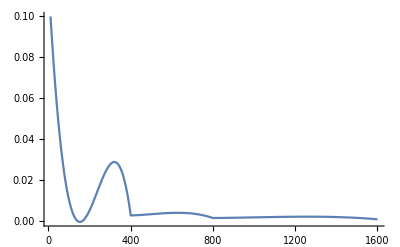

```mathematica
Plot[InterpolatingFunction[{{10,1600}},{5,3,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{10,100,200,400,800,1600}},{{1/10},{1/100},{1/200},{1/400},{1/800},{1/1600}},{Automatic}][x],{x,10,1600},PlotRange->All]
```

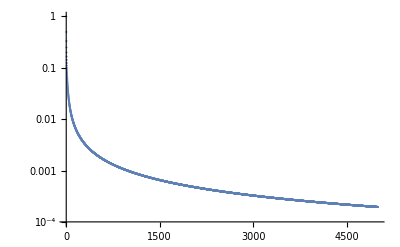

```mathematica
Export[Table[{x,1/x},{x,1,5000}]]
```

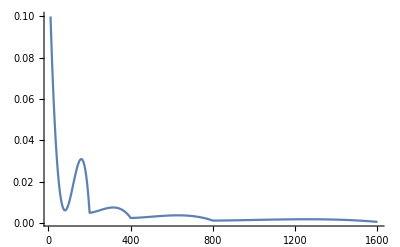

```mathematica
Plot[InterpolatingFunction[{{10,1600}},{5,3,0,{7},{4},0,0,0,0,Automatic,{},{},False},{{10,50,100,200,400,800,1600}},{{1/10},{1/50},{1/100},{1/200},{1/400},{1/800},{1/1600}},{Automatic}][x],{x,10,1600},PlotRange->All]
```

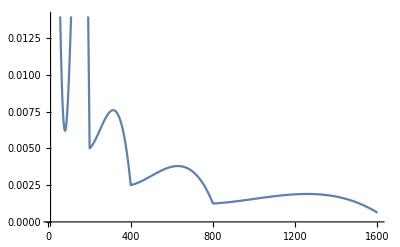

```mathematica
Plot[InterpolatingFunction[{{10,1600}},{5,3,0,{7},{4},0,0,0,0,Automatic,{},{},False},{{10,50,100,200,400,800,1600}},{{1/10},{1/50},{1/100},{1/200},{1/400},{1/800},{1/1600}},{Automatic}][x],{x,10,1600}]
```

```mathematica
Join[{{25,50,100,200,400,800,1600}},{{{1/20},{1/50},{1/60},{1/70},{1/80},{1/90},{1/100}}//Flatten}]
```

{{25,50,100,200,400,800,1600},{1/20,1/50,1/60,1/70,1/80,1/90,1/100}}

```mathematica
Transpose[{{5,10,25,50,100,200,400,800,1600},{0.4,1/10,1/20,1/50,1/60,1/70,1/80,1/90,1/100}}]
```

```mathematica
{{5,0.4},{10,1/14},{25,1/27},{50,1/48},{100,1/59.680},{200,1/74.58},{400,1/84.12},{800,1/92.27},{1600,1/101.9150}}
```

{{5,0.4},{10,1/14},{25,1/27},{50,1/48},{100,0.016756},{200,0.0134084},{400,0.0118878},{800,0.0108378},{1600,0.0098121}}

```mathematica
Interpolation[%47]
```

InterpolatingFunction[…]

```mathematica
%48[10]
```

0.0714286

```mathematica
Clear[a]
```

```mathematica
a:=a=ParallelTable[{z,Abs[%48[z]]},{z,5,1500,5}]
```

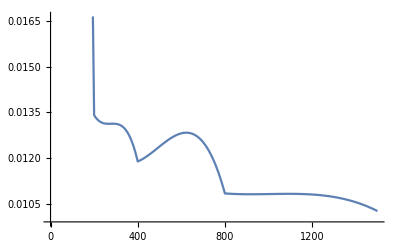

```mathematica
a//ListLinePlot
```

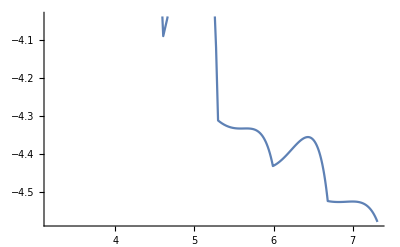

```mathematica
ListPlot[%62,Joined->True]
```

```mathematica
Export["hbn_error_M.dat",ParallelTable[{z,%48[z]},{z,5,1500,25}]]
```

hbn_error_M.dat

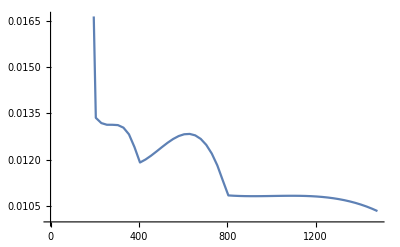

```mathematica
ListLinePlot[ParallelTable[{z,%48[z]},{z,5,1500,25}]]
```

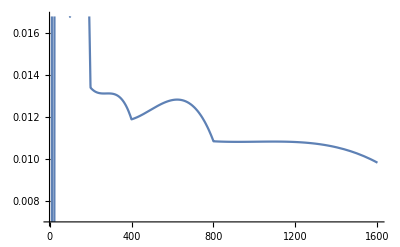

```mathematica
Plot[%48[x],{x,5.,1600.}]
```

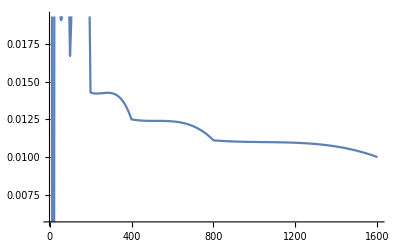

```mathematica
Plot[%43[x],{x,5.,1600.}]
```

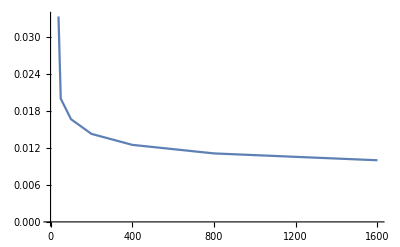

```mathematica
ListPlot[{{25,1/20},{50,1/50},{100,1/60},{200,1/70},{400,1/80},{800,1/90},{1600,1/100}},Joined->True]
```

```mathematica
Table[{x,InterpolatingFunction[{{50,1600}},{5,3,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{25,50,100,200,400,800,1600}},{{1/20},{1/50},{1/60},{1/70},{1/80},{1/90},{1/100}},{Automatic}][x]/2},{x,50,1600}]//ListLogLogPlot
```

-Graphics-

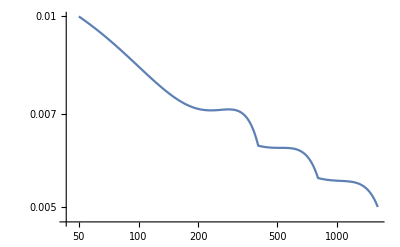

```mathematica
ListLogLogPlot[%27,Joined->True]
```

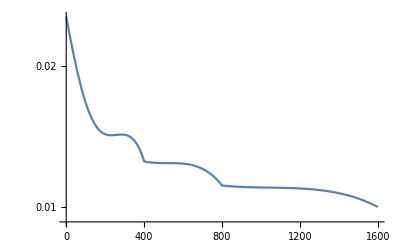

```mathematica
ListLogPlot[%5,Joined->True,PlotRange->All]
```

```mathematica
l1={{10,20/75},{50,5/75+0.02222},{100,2/75}(*,{200,1/200},{400,1/450},{800,1/900},{1600,0},{4000,0},{5000,0}*)}
```

{{10,4/15},{50,0.0888867},{100,2/75}}

```mathematica
m=Transpose[Join[{Log[Transpose[l][[1]]]},{Transpose[l][[2]]}]]
```

{{Log[50],1/15},{Log[100],2/75},{Log[200],1/75},{Log[400],1/150},{Log[800],1/225},{Log[1600],1/300},{Log[4000],0}}

```mathematica
Interpolation[m]
```

InterpolatingFunction[…]

```mathematica
N[l]
```

{{10.,0.266667},{50.,0.0888867},{800.,0.00444444},{1600.,0.00333333},{4000.,0.},{5000.,0.}}

```mathematica
Interpolation[l]
```

InterpolatingFunction[…]

```mathematica
l2:={{100,2/75},{200,1/200},{400,1/450},{800,1/900},{1600,0},{4000,0},{5000,0}}
```

```mathematica
ab:=Join[Table[{x,Interpolation[l1][x]},{x,Range[10,100,1]}],Table[{x,Interpolation[l2][x]},{x,Range[101,1000,1]}],Table[{x,Interpolation[l2][x]},{x,Range[1001,5000,10]}]]
```

```mathematica
ab
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

{{10,0.266667},{11,0.260835},{12,0.255075},{13,0.249386},{14,0.243769},{15,0.238222},{16,0.232746},{17,0.227342},{18,0.222008},{19,0.216746},{20,0.211555},{21,0.206435},{22,0.201386},{23,0.196408},{24,0.191501},{25,0.186665},{26,0.181901},{27,0.177208},{28,0.172585},{29,0.168034},{30,0.163554},{31,0.159145},{32,0.154807},{33,0.150541},{34,0.146345},{35,0.14222},{36,0.138167},{37,0.134185},{38,0.130274},{39,0.126434},{40,0.122665},{41,0.118967},{42,0.11534},{43,0.111785},{44,0.1083},{45,0.104887},{46,0.101545},{47,0.0982734},{48,0.0950734},{49,0.0919445},{50,0.0888867},{51,0.0859},{52,0.0829844},{53,0.08014},{54,0.0773666},{55,0.0746644},{56,0.0720333},{57,0.0694733},{58,0.0669844},{59,0.0645667},{60,0.06222},{61,0.0599445},{62,0.05774},{63,0.0556067},{64,0.0535445},{65,0.0515534},{66,0.0496334},{67,0.0477846},{68,0.0460068},{69,0.0443002},{70,0.0426647},{71,0.0411003},{72,0.039607},{73,0.0381848},{74,0.0368337},{75,0.0355537},{76,0.0343449},{77,0.0332072},{78,0.0321406},{79,0.0311451},{80,0.0302207},{81,0.0293674},{82,0.0285852},{83,0.0278742},{84,0.0272342},{85,0.0266654},{86,0.0261677},{87,0.0257411},{88,0.0253856},{89,0.0251013},{90,0.024888},{91,0.0247459},{92,0.0246748},{93,0.0246749},{94,0.0247461},{95,0.0248884},{96,0.0251018},{97,0.0253864},{98,0.025742},{99,0.0261688},{100,0.0266667},{101,221384381/8400000000},{102,11720699/450000000},{103,648617861/25200000000},{104,5007259/196875000},{105,562927/22400000},{106,11173373/450000000},{107,88311007/3600000000},{108,596384/24609375},{109,28727107/1200000000},{110,198631/8400000},{111,588568333/25200000000},{112,567671/24609375},{113,82010453/3600000000},{114,3374419/150000000},{115,4478261/201600000},{116,154217/7031250},{117,545695559/25200000000},{118,7482333/350000000},{119,59090093/2800000000},{120,4687/225000},{121,74018189/3600000000},{122,63920083/3150000000},{123,24030661/1200000000},{124,972611/49218750},{125,31447/1612800},{126,60598921/3150000000},{127,22774889/1200000000},{128,87761/4687500},{129,465382627/25200000000},{130,65573/3600000},{131,452688113/25200000000},{132,48439/2734375},{133,440187991/25200000000},{134,7750187/450000000},{135,489007/28800000},{136,1098437/65625000},{137,19798399/1200000000},{138,51222587/3150000000},{139,403842617/25200000000},{140,3109/196875},{141,18671843/1200000000},{142,6898439/450000000},{143,380563501/25200000000},{144,104593/7031250},{145,328183/22400000},{146,5049959/350000000},{147,358034689/25200000000},{148,98359/7031250},{149,49578401/3600000000},{150,911/67200},{151,48035299/3600000000},{152,2585273/196875000},{153,325628411/25200000000},{154,13349473/1050000000},{155,120073/9600000},{156,86507/7031250},{157,304935599/25200000000},{158,5354911/450000000},{159,32762133/2800000000},{160,9059/787500},{161,284961283/25200000000},{162,5001409/450000000},{163,13106701/1200000000},{164,88036/8203125},{165,303653/28800000},{166,32623741/3150000000},{167,256327109/25200000000},{168,655489/65625000},{169,35304541/3600000000},{170,34657/3600000},{171,238109273/25200000000},{172,3622/390625},{173,25473159/2800000000},{174,28112129/3150000000},{175,14117/1612800},{176,30176/3515625},{177,10098439/1200000000},{178,25984367/3150000000},{179,29103511/3600000000},{180,3119/393750},{181,65183021/8400000000},{182,7980151/1050000000},{183,26791363/3600000000},{184,204907/28125000},{185,1437559/201600000},{186,348877/50000000},{187,172013929/25200000000},{188,328583/49218750},{189,164495567/25200000000},{190,7657/1200000},{191,7482793/1200000000},{192,599689/98437500},{193,21420293/3600000000},{194,18300439/3150000000},{195,381079/67200000},{196,136177/24609375},{197,19432177/3600000000},{198,2368651/450000000},{199,14366973/2800000000},{200,1/200},{201,122736043/25200000000},{202,14938843/3150000000},{203,116323961/25200000000},{204,5263/1171875},{205,125789/28800000},{206,13374161/3150000000},{207,14851307/3600000000},{208,65731/16406250},{209,32668049/8400000000},{210,95083/25200000},{211,13171319/3600000000},{212,24931/7031250},{213,9615919/2800000000},{214,1495907/450000000},{215,648281/201600000},{216,612001/196875000},{217,25224553/8400000000},{218,434807/150000000},{219,10065391/3600000000},{220,1061/393750},{221,9340889/3600000000},{222,2621011/1050000000},{223,60457981/25200000000},{224,226747/98437500},{225,509/230400},{226,105817/50000000},{227,5669641/2800000000},{228,6802/3515625},{229,46521527/25200000000},{230,44321/25200000},{231,14051671/8400000000},{232,44669/28125000},{233,5418013/3600000000},{234,4482859/3150000000},{235,12889/9600000},{236,10364/8203125},{237,29876479/25200000000},{238,3493537/3150000000},{239,3721931/3600000000},{240,3/3125},{241,22363603/25200000000},{242,367289/450000000},{243,18805601/25200000000},{244,11117/16406250},{245,41009/67200000},{246,244883/450000000},{247,1725827/3600000000},{248,81877/196875000},{249,424367/1200000000},{250,59/201600},{251,5869993/25200000000},{252,8587/49218750},{253,46897/400000000},{254,3063/50000000},{255,1313/201600000},{256,-661/14062500},{257,-2502301/25200000000},{258,-157891/1050000000},{259,-5045903/25200000000},{260,-7/28125},{261,-1066831/3600000000},{262,-359729/1050000000},{263,-465199/1200000000},{264,-84961/196875000},{265,-95609/201600000},{266,-1624709/3150000000},{267,-222457/400000000},{268,-2093/3515625},{269,-15961313/25200000000},{270,-2413/3600000},{271,-5930609/8400000000},{272,-12151/16406250},{273,-19507469/25200000000},{274,-362903/450000000},{275,-193/230400},{276,-14237/16406250},{277,-3228383/3600000000},{278,-2912683/3150000000},{279,-23976523/25200000000},{280,-171/175000},{281,-400699/400000000},{282,-461371/450000000},{283,-26402359/25200000000},{284,-7517/7031250},{285,-73207/67200000},{286,-3492199/3150000000},{287,-28395971/25200000000},{288,-16087/14062500},{289,-1392073/1200000000},{290,-9871/8400000},{291,-4280921/3600000000},{292,-29584/24609375},{293,-30595849/25200000000},{294,-428779/350000000},{295,-35569/28800000},{296,-34987/28125000},{297,-31548661/25200000000},{298,-188833/150000000},{299,-10624781/8400000000},{300,-2/1575},{301,-32101057/25200000000},{302,-574601/450000000},{303,-1534759/1200000000},{304,-31502/24609375},{305,-36871/28800000},{306,-4030289/3150000000},{307,-3577639/2800000000},{308,-6973/5468750},{309,-4577279/3600000000},{310,-4561/3600000},{311,-31789867/25200000000},{312,-11767/9375000},{313,-31446629/25200000000},{314,-3905101/3150000000},{315,-248099/201600000},{316,-2861/2343750},{317,-1451821/1200000000},{318,-3774103/3150000000},{319,-4267909/3600000000},{320,-923/787500},{321,-3241653/2800000000},{322,-3599017/3150000000},{323,-4055417/3600000000},{324,-3901/3515625},{325,-587/537600},{326,-160999/150000000},{327,-26559131/25200000000},{328,-203513/196875000},{329,-25519573/25200000000},{330,-1189/1200000},{331,-3485441/3600000000},{332,-23249/24609375},{333,-3313687/3600000000},{334,-313399/350000000},{335,-19479/22400000},{336,-41491/49218750},{337,-2936203/3600000000},{338,-354359/450000000},{339,-6371861/8400000000},{340,-41/56250},{341,-17601497/25200000000},{342,-2102027/3150000000},{343,-5337433/8400000000},{344,-5651/9375000},{345,-16399/28800000},{346,-1686269/3150000000},{347,-1801873/3600000000},{348,-2543/5468750},{349,-10805393/25200000000},{350,-79/201600},{351,-1275301/3600000000},{352,-1481/4687500},{353,-2326463/8400000000},{354,-106783/450000000},{355,-39707/201600000},{356,-3838/24609375},{357,-960067/8400000000},{358,-32389/450000000},{359,-104429/3600000000},{360,23/1575000},{361,23541/400000000},{362,36307/350000000},{363,3760921/25200000000},{364,4808/24609375},{365,6973/28800000},{366,43421/150000000},{367,8503309/25200000000},{368,1357/3515625},{369,10965587/25200000000},{370,4073/8400000},{371,4495691/8400000000},{372,4121/7031250},{373,2295233/3600000000},{374,2172229/3150000000},{375,19/25600},{376,156581/196875000},{377,21395419/25200000000},{378,2845267/3150000000},{379,1149637/1200000000},{380,19/18750},{381,26942863/25200000000},{382,506479/450000000},{383,29795741/25200000000},{384,40679/32812500},{385,261599/201600000},{386,610193/450000000},{387,5093447/3600000000},{388,4031/2734375},{389,613609/400000000},{390,40177/25200000},{391,41708453/25200000000},{392,337903/196875000},{393,2133631/1200000000},{394,828077/450000000},{395,383597/201600000},{396,6911/3515625},{397,17045813/8400000000},{398,2197819/1050000000},{399,54368557/25200000000},{400,1/450},{401,8234549/3600000000},{402,823527/350000000},{403,8708023/3600000000},{404,122321/49218750},{405,514483/201600000},{406,2750087/1050000000},{407,3223969/1200000000},{408,77471/28125000},{409,71133947/25200000000},{410,10409/3600000},{411,24867011/8400000000},{412,149117/49218750},{413,78103471/25200000000},{414,1426207/450000000},{415,10367/3200000},{416,36207/10937500},{417,12172837/3600000000},{418,10875847/3150000000},{419,88811537/25200000000},{420,236/65625},{421,13206289/3600000000},{422,1683419/450000000},{423,96106181/25200000000},{424,36439/9375000},{425,2129/537600},{426,12706571/3150000000},{427,103514969/25200000000},{428,14702/3515625},{429,1702529/400000000},{430,109141/25200000},{431,15861259/3600000000},{432,110276/24609375},{433,38274097/8400000000},{434,4863653/1050000000},{435,135587/28800000},{436,33637/7031250},{437,122476679/25200000000},{438,740497/150000000},{439,126335317/25200000000},{440,8017/1575000},{441,130213403/25200000000},{442,262221/50000000},{443,2128727/400000000},{444,265751/49218750},{445,157741/28800000},{446,17498281/3150000000},{447,47317663/8400000000},{448,562201/98437500},{449,20842501/3600000000},{450,169/28800},{451,49951931/8400000000},{452,7061/1171875},{453,153826711/25200000000},{454,19477069/3150000000},{455,1262473/201600000},{456,19817/3125000},{457,23114557/3600000000},{458,20475227/3150000000},{459,23686271/3600000000},{460,437/65625},{461,56604661/8400000000},{462,21477713/3150000000},{463,24833003/3600000000},{464,49063/7031250},{465,474277/67200000},{466,3211913/450000000},{467,181881409/25200000000},{468,359173/49218750},{469,20656943/2800000000},{470,2983/400000},{471,27135139/3600000000},{472,1499713/196875000},{473,27711533/3600000000},{474,8166593/1050000000},{475,12673/1612800},{476,390689/49218750},{477,28864217/3600000000},{478,1214677/150000000},{479,68693759/8400000000},{480,929/112500},{481,210109763/25200000000},{482,26515303/3150000000},{483,23792649/2800000000},{484,30154/3515625},{485,249317/28800000},{486,27519901/3150000000},{487,10579249/1200000000},{488,583769/65625000},{489,226168267/25200000000},{490,228167/25200000},{491,32880479/3600000000},{492,10796/1171875},{493,234148351/25200000000},{494,4216727/450000000},{495,1904977/201600000},{496,26053/2734375},{497,26898171/2800000000},{498,4358201/450000000},{499,35147351/3600000000},{500,31/3150},{501,11903083/1200000000},{502,31490693/3150000000},{503,253882261/25200000000},{504,1998709/196875000},{505,98203/9600000},{506,1545991/150000000},{507,261665449/25200000000},{508,73549/7031250},{509,265528847/25200000000},{510,29717/2800000},{511,269371933/25200000000},{512,151387/14062500},{513,39027653/3600000000},{514,11462333/1050000000},{515,105521/9600000},{516,272347/24609375},{517,280767959/25200000000},{518,35330797/3150000000},{519,13548497/1200000000},{520,2557/225000},{521,288242923/25200000000},{522,5180269/450000000},{523,32437809/2800000000},{524,31877/2734375},{525,18919/1612800},{526,5311303/450000000},{527,42749867/3600000000},{528,196001/16406250},{529,43265461/3600000000},{530,304651/25200000},{531,306435713/25200000000},{532,200659/16406250},{533,14760971/1200000000},{534,5566787/450000000},{535,2507929/201600000},{536,351823/28125000},{537,35218531/2800000000},{538,39836387/3150000000},{539,320406217/25200000000},{540,719/56250},{541,15419443/1200000000},{542,13562291/1050000000},{543,46738843/3600000000},{544,1284527/98437500},{545,2643967/201600000},{546,13839277/1050000000},{547,47682727/3600000000},{548,46792/3515625},{549,337020407/25200000000},{550,43/3200},{551,37802077/2800000000},{552,2670323/196875000},{553,343372811/25200000000},{554,6159517/450000000},{555,131993/9600000},{556,339862/24609375},{557,49934857/3600000000},{558,43882177/3150000000},{559,117519599/8400000000},{560,922/65625},{561,50789269/3600000000},{562,6374809/450000000},{563,358441121/25200000000},{564,11157/781250},{565,2890451/201600000},{566,45339941/3150000000},{567,364119509/25200000000},{568,135977/9375000},{569,17470447/1200000000},{570,368239/25200000},{571,52797839/3600000000},{572,724447/49218750},{573,124078277/8400000000},{574,46692329/3150000000},{575,3427/230400},{576,209879/14062500},{577,41929291/2800000000},{578,751209/50000000},{579,379840177/25200000000},{580,2977/196875},{581,382256663/25200000000},{582,2282393/150000000},{583,54944563/3600000000},{584,3013799/196875000},{585,442177/28800000},{586,16167817/1050000000},{587,129711443/8400000000},{588,381079/24609375},{589,55899881/3600000000},{590,56051/3600000},{591,43710917/2800000000},{592,110051/7031250},{593,395430451/25200000000},{594,49552639/3150000000},{595,1059719/67200000},{596,37049/2343750},{597,57041377/3600000000},{598,50026357/3150000000},{599,57302051/3600000000},{600,67/4200},{601,402867643/25200000000},{602,50464643/3150000000},{603,57792623/3600000000},{604,12567/781250},{605,361027/22400000},{606,7266623/450000000},{607,407687549/25200000000},{608,1595411/98437500},{609,136381249/8400000000},{610,58549/3600000},{611,58646119/3600000000},{612,401546/24609375},{613,19610651/1200000000},{614,17185183/1050000000},{615,3304361/201600000},{616,3231451/196875000},{617,59169437/3600000000},{618,822869/50000000},{619,415245337/25200000000},{620,464/28125},{621,416221823/25200000000},{622,17361611/1050000000},{623,139038127/8400000000},{624,58249/3515625},{625,3821/230400},{626,52286671/3150000000},{627,19935389/1200000000},{628,818303/49218750},{629,419277127/25200000000},{630,419561/25200000},{631,6663851/400000000},{632,52091/3125000},{633,420278491/25200000000},{634,7508437/450000000},{635,3365149/201600000},{636,273953/16406250},{637,420916879/25200000000},{638,7518191/450000000},{639,60156731/3600000000},{640,4387/262500},{641,20056343/1200000000},{642,52648823/3150000000},{643,421174001/25200000000},{644,411263/24609375},{645,53469/3200000},{646,7517483/450000000},{647,420865189/25200000000},{648,469561/28125000},{649,140187769/8400000000},{650,1121/67200},{651,420161593/25200000000},{652,58583/3515625},{653,59951273/3600000000},{654,17473723/1050000000},{655,478919/28800000},{656,817799/49218750},{657,418346099/25200000000},{658,5804903/350000000},{659,6627519/400000000},{660,931/56250},{661,416615783/25200000000},{662,7430659/450000000},{663,138530407/8400000000},{664,3242489/196875000},{665,3315671/201600000},{666,7390213/450000000},{667,19677029/1200000000},{668,268591/16406250},{669,58838041/3600000000},{670,411149/25200000},{671,410403773/25200000000},{672,177791/10937500},{673,58404133/3600000000},{674,7285697/450000000},{675,26057/1612800},{676,18892/1171875},{677,135112573/8400000000},{678,50549117/3150000000},{679,403419077/25200000000},{680,3593/225000},{681,19113503/1200000000},{682,50040203/3150000000},{683,57032863/3600000000},{684,388778/24609375},{685,352851/22400000},{686,5496889/350000000},{687,56366347/3600000000},{688,54872/3515625},{689,392050067/25200000000},{690,18607/1200000},{691,389413153/25200000000},{692,757907/49218750},{693,386652551/25200000000},{694,2293009/150000000},{695,146197/9600000},{696,2986541/196875000},{697,54393677/3600000000},{698,47400307/3150000000},{699,41957473/2800000000},{700,47/3150},{701,53478649/3600000000},{702,6654799/450000000},{703,123651487/8400000000},{704,68677/4687500},{705,2939423/201600000},{706,45701911/3150000000},{707,363769649/25200000000},{708,16829/1171875},{709,51425521/3600000000},{710,358033/25200000},{711,50864819/3600000000},{712,307327/21875000},{713,39110419/2800000000},{714,43739099/3150000000},{715,397483/28800000},{716,48221/3515625},{717,114488053/8400000000},{718,6093671/450000000},{719,338992237/25200000000},{720,5261/393750},{721,111460241/8400000000},{722,1976323/150000000},{723,47089783/3600000000},{724,639061/49218750},{725,2969/230400},{726,4475469/350000000},{727,319697269/25200000000},{728,2477537/196875000},{729,44930861/3600000000},{730,14851/1200000},{731,103063171/8400000000},{732,85511/7031250},{733,303716591/25200000000},{734,37615609/3150000000},{735,794923/67200000},{736,164749/14062500},{737,41760997/3600000000},{738,36173287/3150000000},{739,4546159/400000000},{740,246/21875},{741,280338103/25200000000},{742,34655773/3150000000},{743,39159443/3600000000},{744,100799/9375000},{745,2141927/201600000},{746,4723133/450000000},{747,261211289/25200000000},{748,83948/8203125},{749,84842069/8400000000},{750,287/28800},{751,35383499/3600000000},{752,238481/24609375},{753,3820397/400000000},{754,29640719/3150000000},{755,1868213/201600000},{756,448999/49218750},{757,10771819/1200000000},{758,1324337/150000000},{759,218728597/25200000000},{760,1919/225000},{761,211086683/25200000000},{762,8633521/1050000000},{763,203281321/25200000000},{764,55613/7031250},{765,223213/28800000},{766,2656449/350000000},{767,2971043/400000000},{768,715021/98437500},{769,178873187/25200000000},{770,174659/25200000},{771,8114413/1200000000},{772,23173/3515625},{773,161763031/25200000000},{774,2810347/450000000},{775,3263/537600},{776,386677/65625000},{777,143971819/25200000000},{778,2489581/450000000},{779,19259711/3600000000},{780,113/21875},{781,17927209/3600000000},{782,15095153/3150000000},{783,115988141/25200000000},{784,72377/16406250},{785,40499/9600000},{786,1810793/450000000},{787,96454529/25200000000},{788,25519/7031250},{789,28806989/8400000000},{790,81337/25200000},{791,76208053/25200000000},{792,79279/28125000},{793,1044677/400000000},{794,840971/350000000},{795,63131/28800000},{796,97429/49218750},{797,44481839/25200000000},{798,1626419/1050000000},{799,4791451/3600000000},{800,1/900},{801,269201477/241920000000},{802,1604797/1440000000},{803,30001471/26880000000},{804,4225367/3780000000},{805,722231/645120000},{806,1614599/1440000000},{807,38810213/34560000000},{808,7381/6562500},{809,12977033/11520000000},{810,54589/48384000},{811,91125029/80640000000},{812,475361/420000000},{813,39177647/34560000000},{814,1635011/1440000000},{815,733661/645120000},{816,9611/8437500},{817,10222703/8960000000},{818,11519251/10080000000},{819,276913703/241920000000},{820,1651/1440000},{821,1469973/1280000000},{822,34785547/30240000000},{823,13273639/11520000000},{824,90889/78750000},{825,89497/77414400},{826,3890941/3360000000},{827,13362851/11520000000},{828,627443/540000000},{829,93857171/80640000000},{830,4477/3840000},{831,282532907/241920000000},{832,5758/4921875},{833,94501303/80640000000},{834,5071303/4320000000},{835,289/245760},{836,1484261/1260000000},{837,40782023/34560000000},{838,11915521/10080000000},{839,31830347/26880000000},{840,1121/945000},{841,13689577/11520000000},{842,1714217/1440000000},{843,288497999/241920000000},{844,23893/20000000},{845,772063/645120000},{846,36254959/30240000000},{847,96852617/80640000000},{848,94/78125},{849,41657219/34560000000},{850,779/645120},{851,13935787/11520000000},{852,4580939/3780000000},{853,32634521/26880000000},{854,12260137/10080000000},{855,336889/276480000},{856,13733/11250000},{857,32872549/26880000000},{858,5292739/4320000000},{859,98978581/80640000000},{860,2479/2016000},{861,298026137/241920000000},{862,592409/480000000},{863,14243999/11520000000},{864,73163/59062500},{865,114373/92160000},{866,4177561/3360000000},{867,301341431/241920000000},{868,1572397/1260000000},{869,14402893/11520000000},{870,43289/34560000},{871,11243961/8960000000},{872,884/703125},{873,304719869/241920000000},{874,12720367/10080000000},{875,145/114688},{876,683999/540000000},{877,14619301/11520000000},{878,12815861/10080000000},{879,44022509/34560000000},{880,67/52500},{881,103105319/80640000000},{882,38737177/30240000000},{883,14784779/11520000000},{884,77149/60000000},{885,498641/387072000},{886,1858559/1440000000},{887,104275537/80640000000},{888,306071/236250000},{889,34889797/26880000000},{890,14981/11520000},{891,45027881/34560000000},{892,1644743/1260000000},{893,5022023/3840000000},{894,39623191/30240000000},{895,846893/645120000},{896,12947/9843750},{897,45541043/34560000000},{898,211237/160000000},{899,106664861/80640000000},{900,229/172800},{901,107068859/80640000000},{902,1489881/1120000000},{903,322423139/241920000000},{904,7511/5625000},{905,123293/92160000},{906,40532029/30240000000},{907,5156657/3840000000},{908,1695227/1260000000},{909,326098793/241920000000},{910,21781/16128000},{911,5195749/3840000000},{912,5719/4218750},{913,109523143/80640000000},{914,1959461/1440000000},{915,2638483/1935360000},{916,573667/420000000},{917,110351627/80640000000},{918,5922829/4320000000},{919,15823943/11520000000},{920,289/210000},{921,47650571/34560000000},{922,13924199/10080000000},{923,111602773/80640000000},{924,5241197/3780000000},{925,569/409600},{926,2004139/1440000000},{927,337325771/241920000000},{928,3929/2812500},{929,12540319/8960000000},{930,339221/241920000},{931,113284669/80640000000},{932,253339/180000000},{933,48731687/34560000000},{934,4746619/3360000000},{935,26087/18432000},{936,83747/59062500},{937,114554687/80640000000},{938,4781957/3360000000},{939,49276889/34560000000},{940,2057/1440000},{941,115404739/80640000000},{942,6193801/4320000000},{943,38610211/26880000000},{944,28331/19687500},{945,2790169/1935360000},{946,2079829/1440000000},{947,5556377/3840000000},{948,5479571/3780000000},{949,16730173/11520000000},{950,4693/3225600},{951,352616627/241920000000},{952,12777/8750000},{953,16852409/11520000000},{954,6331123/4320000000},{955,947161/645120000},{956,29417/20000000},{957,356470841/241920000000},{958,14879741/10080000000},{959,119252281/80640000000},{960,1/675},{961,5699099/3840000000},{962,14986939/10080000000},{963,51475697/34560000000},{964,1880069/1260000000},{965,321437/215040000},{966,45282499/30240000000},{967,17281111/11520000000},{968,8453/5625000},{969,364189853/241920000000},{970,5791/3840000},{971,121825349/80640000000},{972,5720609/3780000000},{973,122253923/80640000000},{974,728977/480000000},{975,673/442368},{976,7501/4921875},{977,17587201/11520000000},{978,46246633/30240000000},{979,13726469/8960000000},{980,15469/10080000},{981,53128151/34560000000},{982,2217487/1440000000},{983,13821417/8960000000},{984,52151/33750000},{985,199711/129024000},{986,15629063/10080000000},{987,375736511/241920000000},{988,93347/60000000},{989,17953013/11520000000},{990,377651/241920000},{991,18013727/11520000000},{992,10279/6562500},{993,379561349/241920000000},{994,15841547/10080000000},{995,145079/92160000},{996,851489/540000000},{997,42455689/26880000000},{998,2278183/1440000000},{999,383367683/241920000000},{1000,1/630},{1001,42736853/26880000000},{1011,390909287/241920000000},{1021,132367699/80640000000},{1031,19199767/11520000000},{1041,409167317/241920000000},{1051,6587329/3840000000},{1061,20032397/11520000000},{1071,426185147/241920000000},{1081,143832719/80640000000},{1091,16170421/8960000000},{1101,63068111/34560000000},{1111,148702129/80640000000},{1121,21451057/11520000000},{1131,64936601/34560000000},{1141,16975571/8960000000},{1151,153935609/80640000000},{1161,464937437/241920000000},{1171,22272107/11520000000},{1181,52235473/26880000000},{1191,67447781/34560000000},{1201,22559137/11520000000},{1211,158307829/80640000000},{1221,475661297/241920000000},{1231,52881923/26880000000},{1241,22653977/11520000000},{1251,475031927/241920000000},{1261,22562597/11520000000},{1271,7493069/3840000000},{1281,469760357/241920000000},{1291,155629189/80640000000},{1301,154475659/80640000000},{1311,65622941/34560000000},{1321,50518933/26880000000},{1331,21397067/11520000000},{1341,63335231/34560000000},{1351,145559009/80640000000},{1361,15900431/8960000000},{1371,421232447/241920000000},{1381,19639117/11520000000},{1391,134286889/80640000000},{1401,56076011/34560000000},{1411,2018083/1280000000},{1421,123166499/80640000000},{1431,356759507/241920000000},{1441,114393239/80640000000},{1451,5218129/3840000000},{1461,313428737/241920000000},{1471,14153407/11520000000},{1481,13338217/11520000000},{1491,262053767/241920000000},{1501,27006353/26880000000},{1511,74364929/80640000000},{1521,28878371/34560000000},{1531,60066869/80640000000},{1541,2495759/3840000000},{1551,19032461/34560000000},{1561,36055279/80640000000},{1571,27343549/80640000000},{1581,54803657/241920000000},{1591,420109/3840000000},{1601,-2718067/3225600000000},{1611,-89059531/9676800000000},{1621,-2679547/153600000000},{1631,-82471997/3225600000000},{1641,-46411303/1382400000000},{1651,-14859513/358400000000},{1661,-7561987/153600000000},{1671,-550480111/9676800000000},{1681,-23090283/358400000000},{1691,-33108751/460800000000},{1701,-766024501/9676800000000},{1711,-13264537/153600000000},{1721,-301404587/3225600000000},{1731,-138810613/1382400000000},{1741,-38446423/358400000000},{1751,-122595239/1075200000000},{1761,-166798783/1382400000000},{1771,-45583793/358400000000},{1781,-61565521/460800000000},{1791,-1353938071/9676800000000},{1801,-22443727/153600000000},{1811,-490977377/3225600000000},{1821,-1530876061/9676800000000},{1831,-8401019/51200000000},{1841,-60877323/358400000000},{1851,-242652493/1382400000000},{1861,-64905103/358400000000},{1871,-85966891/460800000000},{1881,-1857174241/9676800000000},{1891,-212005819/1075200000000},{1901,-93235481/460800000000},{1911,-2006858431/9676800000000},{1921,-10871949/51200000000},{1931,-233530099/1075200000000},{1941,-306826003/1382400000000},{1951,-81216213/358400000000},{1961,-745648027/3225600000000},{1971,-325729573/1382400000000},{1981,-258036949/1075200000000},{1991,-112553651/460800000000},{2001,-2403995401/9676800000000},{2011,-12928279/51200000000},{2021,-275775629/1075200000000},{2031,-2519609191/9676800000000},{2041,-13525589/51200000000},{2051,-864056017/3225600000000},{2061,-375301483/1382400000000},{2071,-295685479/1075200000000},{2081,-128302421/460800000000},{2091,-2726660971/9676800000000},{2101,-102152063/358400000000},{2111,-14754979/51200000000},{2121,-2818422961/9676800000000},{2131,-15065119/51200000000},{2141,-958450207/3225600000000},{2151,-414651193/1382400000000},{2161,-325437409/1075200000000},{2171,-984830537/3225600000000},{2181,-425604163/1382400000000},{2191,-111227973/358400000000},{2201,-48036127/153600000000},{2211,-3048597331/9676800000000},{2221,-16244049/51200000000},{2231,-1030288597/3225600000000},{2241,-3110824921/9676800000000},{2251,-49682677/153600000000},{2261,-1049474327/3225600000000},{2271,-452296273/1382400000000},{2281,-117887683/358400000000},{2291,-50779517/153600000000},{2301,-3214506301/9676800000000},{2311,-119598653/358400000000},{2321,-154432741/460800000000},{2331,-3256284091/9676800000000},{2341,-51885067/153600000000},{2351,-1093506317/3225600000000},{2361,-470224183/1382400000000},{2371,-122293193/358400000000},{2381,-122650583/358400000000},{2391,-474360553/1382400000000},{2401,-123288763/358400000000},{2411,-158875711/460800000000},{2421,-3343309861/9676800000000},{2431,-53167657/153600000000},{2441,-1118384507/3225600000000},{2451,-3360089251/9676800000000},{2461,-17800929/51200000000},{2471,-374224279/1075200000000},{2481,-481574863/1382400000000},{2491,-124940673/358400000000},{2501,-160721281/460800000000},{2511,-3376276231/9676800000000},{2521,-375199129/1075200000000},{2531,-160795271/460800000000},{2541,-3376007821/9676800000000},{2551,-17855659/51200000000},{2561,-374760209/1075200000000},{2571,-481482973/1382400000000},{2581,-124716383/358400000000},{2591,-1121244157/3225600000000},{2601,-479936743/1382400000000},{2611,-372758059/1075200000000},{2621,-159501641/460800000000},{2631,-3343698991/9676800000000},{2641,-17657789/51200000000},{2651,-123348513/358400000000},{2661,-3322968181/9676800000000},{2671,-17539699/51200000000},{2681,-1102173547/3225600000000},{2691,-471075253/1382400000000},{2701,-365336389/1075200000000},{2711,-156096611/460800000000},{2721,-3267536761/9676800000000},{2731,-120613233/358400000000},{2741,-51509467/153600000000},{2751,-3233160151/9676800000000},{2761,-17041029/51200000000},{2771,-1069295137/3225600000000},{2781,-456365563/1382400000000},{2791,-353420119/1075200000000},{2801,-1055519267/3225600000000},{2811,-450270733/1382400000000},{2821,-116177743/358400000000},{2831,-49544057/153600000000},{2841,-3105330721/9676800000000},{2851,-16343759/51200000000},{2861,-1024066927/3225600000000},{2871,-3055027711/9676800000000},{2881,-48213607/153600000000},{2891,-1006498457/3225600000000},{2901,-428735443/1382400000000},{2911,-110460053/358400000000},{2921,-15678949/51200000000},{2931,-2943853891/9676800000000},{2941,-108297223/358400000000},{2951,-138278131/460800000000},{2961,-2883307081/9676800000000},{2971,-45435397/153600000000},{2981,-947071847/3225600000000},{2991,-402809953/1382400000000},{3001,-103622163/358400000000},{3011,-308400859/1075200000000},{3021,-393300523/1382400000000},{3031,-101121933/358400000000},{3041,-128913301/460800000000},{3051,-2683771051/9676800000000},{3061,-42223387/153600000000},{3071,-878697437/3225600000000},{3081,-2611833841/9676800000000},{3091,-13689439/51200000000},{3101,-284723189/1075200000000},{3111,-362493433/1382400000000},{3121,-93042443/358400000000},{3131,-118409071/460800000000},{3141,-2460793621/9676800000000},{3151,-270529039/1075200000000},{3161,-114690461/460800000000},{3171,-2382014611/9676800000000},{3181,-12461969/51200000000},{3191,-86236973/358400000000},{3201,-328754143/1382400000000},{3211,-84220753/358400000000},{3221,-748816087/3225600000000},{3231,-316964113/1382400000000},{3241,-243429769/1075200000000},{3251,-102991031/460800000000},{3261,-2134585981/9676800000000},{3271,-11143899/51200000000},{3281,-230850049/1075200000000},{3291,-2048952571/9676800000000},{3301,-10688409/51200000000},{3311,-663708877/3225600000000},{3321,-280287223/1382400000000},{3331,-214751899/1075200000000},{3341,-90638201/460800000000},{3351,-1873921951/9676800000000},{3361,-68308603/358400000000},{3371,-28803797/153600000000},{3381,-1784848741/9676800000000},{3391,-9285539/51200000000},{3401,-574999867/3225600000000},{3411,-242136133/1382400000000},{3421,-184981429/1075200000000},{3431,-544881797/3225600000000},{3441,-229199503/1382400000000},{3451,-58299713/358400000000},{3461,-8167929/51200000000},{3471,-1513341511/9676800000000},{3481,-7846069/51200000000},{3491,-484147057/3225600000000},{3501,-1421949901/9676800000000},{3511,-22086337/153600000000},{3521,-453638387/3225600000000},{3531,-190054813/1382400000000},{3541,-48142623/358400000000},{3551,-20147977/153600000000},{3561,-1238804881/9676800000000},{3571,-44751993/358400000000},{3581,-56086921/460800000000},{3591,-1147375471/9676800000000},{3601,-17729527/153600000000},{3611,-362195177/3225600000000},{3621,-150893923/1382400000000},{3631,-37999333/358400000000},{3641,-110640569/1075200000000},{3651,-137944693/1382400000000},{3661,-34649303/358400000000},{3671,-43120291/460800000000},{3681,-875603641/9676800000000},{3691,-13424917/153600000000},{3701,-272010167/3225600000000},{3711,-786391831/9676800000000},{3721,-4004549/51200000000},{3731,-26942233/358400000000},{3741,-99734203/1382400000000},{3751,-24776413/358400000000},{3761,-30472261/460800000000},{3771,-611008411/9676800000000},{3781,-64693549/1075200000000},{3791,-26363051/460800000000},{3801,-525160801/9676800000000},{3811,-2628879/51200000000},{3821,-52080229/1075200000000},{3831,-62965513/1382400000000},{3841,-15295323/358400000000},{3851,-128457817/3225600000000},{3861,-51137683/1382400000000},{3871,-36750079/1075200000000},{3881,-14463821/460800000000},{3891,-276938371/9676800000000},{3901,-1324609/51200000000},{3911,-24887159/1075200000000},{3921,-197844361/9676800000000},{3931,-909719/51200000000},{3941,-48756007/3225600000000},{3951,-17263393/1382400000000},{3961,-10630009/1075200000000},{3971,-3369191/460800000000},{3981,-46098541/9676800000000},{3991,-804173/358400000000},{4001,12691/51200000000},{4011,26229269/9676800000000},{4021,263351/51200000000},{4031,24341603/3225600000000},{4041,13711097/1382400000000},{4051,13180661/1075200000000},{4061,46987873/3225600000000},{4071,23283527/1382400000000},{4081,6840117/358400000000},{4091,3270683/153600000000},{4101,227088299/9676800000000},{4111,1311021/51200000000},{4121,89377013/3225600000000},{4131,288126509/9676800000000},{4141,4885133/153600000000},{4151,109011883/3225600000000},{4161,49419617/1382400000000},{4171,13498607/358400000000},{4181,6073093/153600000000},{4191,400358729/9676800000000},{4201,15471037/358400000000},{4211,20698889/460800000000},{4221,451228739/9676800000000},{4231,7418543/153600000000},{4241,161029693/3225600000000},{4251,71197907/1382400000000},{4261,19009297/358400000000},{4271,19543707/358400000000},{4281,77380937/1382400000000},{4291,20563127/358400000000},{4301,27061319/460800000000},{4311,580910369/9676800000000},{4321,9413753/153600000000},{4331,201583303/3225600000000},{4341,615954779/9676800000000},{4351,3315741/51200000000},{4361,70767191/1075200000000},{4371,92376827/1382400000000},{4381,24291417/358400000000},{4391,31647149/460800000000},{4401,672797399/9676800000000},{4411,75609341/1075200000000},{4421,32744959/460800000000},{4431,694271609/9676800000000},{4441,3705611/51200000000},{4451,78433861/1075200000000},{4461,101556917/1382400000000},{4471,26493907/358400000000},{4481,239736653/3225600000000},{4491,103216547/1382400000000},{4501,80583011/1075200000000},{4511,34637989/460800000000},{4521,728961839/9676800000000},{4531,3862081/51200000000},{4541,27048377/358400000000},{4551,730074449/9676800000000},{4561,3858371/51200000000},{4571,242591063/3225600000000},{4581,103670237/1382400000000},{4591,80331281/1075200000000},{4601,34268419/460800000000},{4611,715651469/9676800000000},{4621,26334057/358400000000},{4631,11202143/153600000000},{4641,699791879/9676800000000},{4651,3667641/51200000000},{4661,228635273/3225600000000},{4671,96850127/1382400000000},{4681,74368151/1075200000000},{4691,219995743/3225600000000},{4701,92852357/1382400000000},{4711,23675747/358400000000},{4721,9965353/153600000000},{4731,615676709/9676800000000},{4741,3189511/51200000000},{4751,196411283/3225600000000},{4761,574919519/9676800000000},{4771,8886803/153600000000},{4781,181358353/3225600000000},{4791,75361847/1382400000000},{4801,18897637/358400000000},{4811,2604121/51200000000},{4821,473354939/9676800000000},{4831,16805867/358400000000},{4841,20637299/460800000000},{4851,412223549/9676800000000},{4861,6194813/153600000000},{4871,122508763/3225600000000},{4881,49139537/1382400000000},{4891,11837727/358400000000},{4901,32716211/1075200000000},{4911,38350367/1382400000000},{4921,8949357/358400000000},{4931,10189529/460800000000},{4941,185488979/9676800000000},{4951,2478623/153600000000},{4961,41988973/3225600000000},{4971,94923989/9676800000000},{4981,333431/51200000000},{4991,3360481/1075200000000}}

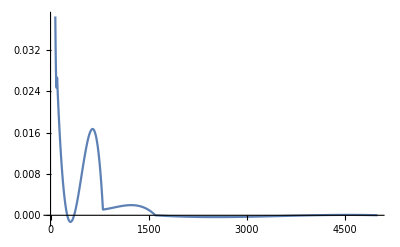

```mathematica
ListPlot[%22,Joined->True]
```

```mathematica
Show[ab,Joined->True,PlotRange->All,FrameTicks->{{Automatic,None},{
{10,1000,2000,3000,4000,5000},None}},FrameLabel->{{HoldForm[ζ],None},{HoldForm[M],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{{10,0.266667},{11,0.260835},{12,0.255075},{13,0.249386},{14,0.243769},{15,0.238222},{16,0.232746},{17,0.227342},{18,0.222008},{19,0.216746},«1381»},Joined→True,PlotRange→All,FrameTicks→{{Automatic,None},{{10,1000,2000,3000,4000,5000},None}},FrameLabel→{{ζ,None},{M,None}},LabelStyle→{FontFamily→Times New Roman,16,GrayLevel[0]},Frame→True].

Show[{{10,0.266667},{11,0.260835},{12,0.255075},{13,0.249386},{14,0.243769},{15,0.238222},{16,0.232746},{17,0.227342},{18,0.222008},{19,0.216746},{20,0.211555},{21,0.206435},{22,0.201386},{23,0.196408},{24,0.191501},{25,0.186665},{26,0.181901},{27,0.177208},{28,0.172585},{29,0.168034},{30,0.163554},{31,0.159145},{32,0.154807},{33,0.150541},{34,0.146345},{35,0.14222},{36,0.138167},{37,0.134185},{38,0.130274},{39,0.126434},{40,0.122665},{41,0.118967},{42,0.11534},{43,0.111785},{44,0.1083},{45,0.104887},{46,0.101545},{47,0.0982734},{48,0.0950734},{49,0.0919445},{50,0.0888867},{51,0.0859},{52,0.0829844},{53,0.08014},{54,0.0773666},{55,0.0746644},{56,0.0720333},{57,0.0694733},{58,0.0669844},{59,0.0645667},{60,0.06222},{61,0.0599445},{62,0.05774},{63,0.0556067},{64,0.0535445},{65,0.0515534},{66,0.0496334},{67,0.0477846},{68,0.0460068},{69,0.0443002},{70,0.0426647},{71,0.0411003},{72,0.039607},{73,0.0381848},{74,0.0368337},{75,0.0355537},{76,0.0343449},{77,0.0332072},{78,0.0321406},{79,0.0311451},{80,0.0302207},{81,0.0293674},{82,0.0285852},{83,0.0278742},{84,0.0272342},{85,0.0266654},{86,0.0261677},{87,0.0257411},{88,0.0253856},{89,0.0251013},{90,0.024888},{91,0.0247459},{92,0.0246748},{93,0.0246749},{94,0.0247461},{95,0.0248884},{96,0.0251018},{97,0.0253864},{98,0.025742},{99,0.0261688},{100,0.0266667},{101,221384381/8400000000},{102,11720699/450000000},{103,648617861/25200000000},{104,5007259/196875000},{105,562927/22400000},{106,11173373/450000000},{107,88311007/3600000000},{108,596384/24609375},{109,28727107/1200000000},{110,198631/8400000},{111,588568333/25200000000},{112,567671/24609375},{113,82010453/3600000000},{114,3374419/150000000},{115,4478261/201600000},{116,154217/7031250},{117,545695559/25200000000},{118,7482333/350000000},{119,59090093/2800000000},{120,4687/225000},{121,74018189/3600000000},{122,63920083/3150000000},{123,24030661/1200000000},{124,972611/49218750},{125,31447/1612800},{126,60598921/3150000000},{127,22774889/1200000000},{128,87761/4687500},{129,465382627/25200000000},{130,65573/3600000},{131,452688113/25200000000},{132,48439/2734375},{133,440187991/25200000000},{134,7750187/450000000},{135,489007/28800000},{136,1098437/65625000},{137,19798399/1200000000},{138,51222587/3150000000},{139,403842617/25200000000},{140,3109/196875},{141,18671843/1200000000},{142,6898439/450000000},{143,380563501/25200000000},{144,104593/7031250},{145,328183/22400000},{146,5049959/350000000},{147,358034689/25200000000},{148,98359/7031250},{149,49578401/3600000000},{150,911/67200},{151,48035299/3600000000},{152,2585273/196875000},{153,325628411/25200000000},{154,13349473/1050000000},{155,120073/9600000},{156,86507/7031250},{157,304935599/25200000000},{158,5354911/450000000},{159,32762133/2800000000},{160,9059/787500},{161,284961283/25200000000},{162,5001409/450000000},{163,13106701/1200000000},{164,88036/8203125},{165,303653/28800000},{166,32623741/3150000000},{167,256327109/25200000000},{168,655489/65625000},{169,35304541/3600000000},{170,34657/3600000},{171,238109273/25200000000},{172,3622/390625},{173,25473159/2800000000},{174,28112129/3150000000},{175,14117/1612800},{176,30176/3515625},{177,10098439/1200000000},{178,25984367/3150000000},{179,29103511/3600000000},{180,3119/393750},{181,65183021/8400000000},{182,7980151/1050000000},{183,26791363/3600000000},{184,204907/28125000},{185,1437559/201600000},{186,348877/50000000},{187,172013929/25200000000},{188,328583/49218750},{189,164495567/25200000000},{190,7657/1200000},{191,7482793/1200000000},{192,599689/98437500},{193,21420293/3600000000},{194,18300439/3150000000},{195,381079/67200000},{196,136177/24609375},{197,19432177/3600000000},{198,2368651/450000000},{199,14366973/2800000000},{200,1/200},{201,122736043/25200000000},{202,14938843/3150000000},{203,116323961/25200000000},{204,5263/1171875},{205,125789/28800000},{206,13374161/3150000000},{207,14851307/3600000000},{208,65731/16406250},{209,32668049/8400000000},{210,95083/25200000},{211,13171319/3600000000},{212,24931/7031250},{213,9615919/2800000000},{214,1495907/450000000},{215,648281/201600000},{216,612001/196875000},{217,25224553/8400000000},{218,434807/150000000},{219,10065391/3600000000},{220,1061/393750},{221,9340889/3600000000},{222,2621011/1050000000},{223,60457981/25200000000},{224,226747/98437500},{225,509/230400},{226,105817/50000000},{227,5669641/2800000000},{228,6802/3515625},{229,46521527/25200000000},{230,44321/25200000},{231,14051671/8400000000},{232,44669/28125000},{233,5418013/3600000000},{234,4482859/3150000000},{235,12889/9600000},{236,10364/8203125},{237,29876479/25200000000},{238,3493537/3150000000},{239,3721931/3600000000},{240,3/3125},{241,22363603/25200000000},{242,367289/450000000},{243,18805601/25200000000},{244,11117/16406250},{245,41009/67200000},{246,244883/450000000},{247,1725827/3600000000},{248,81877/196875000},{249,424367/1200000000},{250,59/201600},{251,5869993/25200000000},{252,8587/49218750},{253,46897/400000000},{254,3063/50000000},{255,1313/201600000},{256,-661/14062500},{257,-2502301/25200000000},{258,-157891/1050000000},{259,-5045903/25200000000},{260,-7/28125},{261,-1066831/3600000000},{262,-359729/1050000000},{263,-465199/1200000000},{264,-84961/196875000},{265,-95609/201600000},{266,-1624709/3150000000},{267,-222457/400000000},{268,-2093/3515625},{269,-15961313/25200000000},{270,-2413/3600000},{271,-5930609/8400000000},{272,-12151/16406250},{273,-19507469/25200000000},{274,-362903/450000000},{275,-193/230400},{276,-14237/16406250},{277,-3228383/3600000000},{278,-2912683/3150000000},{279,-23976523/25200000000},{280,-171/175000},{281,-400699/400000000},{282,-461371/450000000},{283,-26402359/25200000000},{284,-7517/7031250},{285,-73207/67200000},{286,-3492199/3150000000},{287,-28395971/25200000000},{288,-16087/14062500},{289,-1392073/1200000000},{290,-9871/8400000},{291,-4280921/3600000000},{292,-29584/24609375},{293,-30595849/25200000000},{294,-428779/350000000},{295,-35569/28800000},{296,-34987/28125000},{297,-31548661/25200000000},{298,-188833/150000000},{299,-10624781/8400000000},{300,-2/1575},{301,-32101057/25200000000},{302,-574601/450000000},{303,-1534759/1200000000},{304,-31502/24609375},{305,-36871/28800000},{306,-4030289/3150000000},{307,-3577639/2800000000},{308,-6973/5468750},{309,-4577279/3600000000},{310,-4561/3600000},{311,-31789867/25200000000},{312,-11767/9375000},{313,-31446629/25200000000},{314,-3905101/3150000000},{315,-248099/201600000},{316,-2861/2343750},{317,-1451821/1200000000},{318,-3774103/3150000000},{319,-4267909/3600000000},{320,-923/787500},{321,-3241653/2800000000},{322,-3599017/3150000000},{323,-4055417/3600000000},{324,-3901/3515625},{325,-587/537600},{326,-160999/150000000},{327,-26559131/25200000000},{328,-203513/196875000},{329,-25519573/25200000000},{330,-1189/1200000},{331,-3485441/3600000000},{332,-23249/24609375},{333,-3313687/3600000000},{334,-313399/350000000},{335,-19479/22400000},{336,-41491/49218750},{337,-2936203/3600000000},{338,-354359/450000000},{339,-6371861/8400000000},{340,-41/56250},{341,-17601497/25200000000},{342,-2102027/3150000000},{343,-5337433/8400000000},{344,-5651/9375000},{345,-16399/28800000},{346,-1686269/3150000000},{347,-1801873/3600000000},{348,-2543/5468750},{349,-10805393/25200000000},{350,-79/201600},{351,-1275301/3600000000},{352,-1481/4687500},{353,-2326463/8400000000},{354,-106783/450000000},{355,-39707/201600000},{356,-3838/24609375},{357,-960067/8400000000},{358,-32389/450000000},{359,-104429/3600000000},{360,23/1575000},{361,23541/400000000},{362,36307/350000000},{363,3760921/25200000000},{364,4808/24609375},{365,6973/28800000},{366,43421/150000000},{367,8503309/25200000000},{368,1357/3515625},{369,10965587/25200000000},{370,4073/8400000},{371,4495691/8400000000},{372,4121/7031250},{373,2295233/3600000000},{374,2172229/3150000000},{375,19/25600},{376,156581/196875000},{377,21395419/25200000000},{378,2845267/3150000000},{379,1149637/1200000000},{380,19/18750},{381,26942863/25200000000},{382,506479/450000000},{383,29795741/25200000000},{384,40679/32812500},{385,261599/201600000},{386,610193/450000000},{387,5093447/3600000000},{388,4031/2734375},{389,613609/400000000},{390,40177/25200000},{391,41708453/25200000000},{392,337903/196875000},{393,2133631/1200000000},{394,828077/450000000},{395,383597/201600000},{396,6911/3515625},{397,17045813/8400000000},{398,2197819/1050000000},{399,54368557/25200000000},{400,1/450},{401,8234549/3600000000},{402,823527/350000000},{403,8708023/3600000000},{404,122321/49218750},{405,514483/201600000},{406,2750087/1050000000},{407,3223969/1200000000},{408,77471/28125000},{409,71133947/25200000000},{410,10409/3600000},{411,24867011/8400000000},{412,149117/49218750},{413,78103471/25200000000},{414,1426207/450000000},{415,10367/3200000},{416,36207/10937500},{417,12172837/3600000000},{418,10875847/3150000000},{419,88811537/25200000000},{420,236/65625},{421,13206289/3600000000},{422,1683419/450000000},{423,96106181/25200000000},{424,36439/9375000},{425,2129/537600},{426,12706571/3150000000},{427,103514969/25200000000},{428,14702/3515625},{429,1702529/400000000},{430,109141/25200000},{431,15861259/3600000000},{432,110276/24609375},{433,38274097/8400000000},{434,4863653/1050000000},{435,135587/28800000},{436,33637/7031250},{437,122476679/25200000000},{438,740497/150000000},{439,126335317/25200000000},{440,8017/1575000},{441,130213403/25200000000},{442,262221/50000000},{443,2128727/400000000},{444,265751/49218750},{445,157741/28800000},{446,17498281/3150000000},{447,47317663/8400000000},{448,562201/98437500},{449,20842501/3600000000},{450,169/28800},{451,49951931/8400000000},{452,7061/1171875},{453,153826711/25200000000},{454,19477069/3150000000},{455,1262473/201600000},{456,19817/3125000},{457,23114557/3600000000},{458,20475227/3150000000},{459,23686271/3600000000},{460,437/65625},{461,56604661/8400000000},{462,21477713/3150000000},{463,24833003/3600000000},{464,49063/7031250},{465,474277/67200000},{466,3211913/450000000},{467,181881409/25200000000},{468,359173/49218750},{469,20656943/2800000000},{470,2983/400000},{471,27135139/3600000000},{472,1499713/196875000},{473,27711533/3600000000},{474,8166593/1050000000},{475,12673/1612800},{476,390689/49218750},{477,28864217/3600000000},{478,1214677/150000000},{479,68693759/8400000000},{480,929/112500},{481,210109763/25200000000},{482,26515303/3150000000},{483,23792649/2800000000},{484,30154/3515625},{485,249317/28800000},{486,27519901/3150000000},{487,10579249/1200000000},{488,583769/65625000},{489,226168267/25200000000},{490,228167/25200000},{491,32880479/3600000000},{492,10796/1171875},{493,234148351/25200000000},{494,4216727/450000000},{495,1904977/201600000},{496,26053/2734375},{497,26898171/2800000000},{498,4358201/450000000},{499,35147351/3600000000},{500,31/3150},{501,11903083/1200000000},{502,31490693/3150000000},{503,253882261/25200000000},{504,1998709/196875000},{505,98203/9600000},{506,1545991/150000000},{507,261665449/25200000000},{508,73549/7031250},{509,265528847/25200000000},{510,29717/2800000},{511,269371933/25200000000},{512,151387/14062500},{513,39027653/3600000000},{514,11462333/1050000000},{515,105521/9600000},{516,272347/24609375},{517,280767959/25200000000},{518,35330797/3150000000},{519,13548497/1200000000},{520,2557/225000},{521,288242923/25200000000},{522,5180269/450000000},{523,32437809/2800000000},{524,31877/2734375},{525,18919/1612800},{526,5311303/450000000},{527,42749867/3600000000},{528,196001/16406250},{529,43265461/3600000000},{530,304651/25200000},{531,306435713/25200000000},{532,200659/16406250},{533,14760971/1200000000},{534,5566787/450000000},{535,2507929/201600000},{536,351823/28125000},{537,35218531/2800000000},{538,39836387/3150000000},{539,320406217/25200000000},{540,719/56250},{541,15419443/1200000000},{542,13562291/1050000000},{543,46738843/3600000000},{544,1284527/98437500},{545,2643967/201600000},{546,13839277/1050000000},{547,47682727/3600000000},{548,46792/3515625},{549,337020407/25200000000},{550,43/3200},{551,37802077/2800000000},{552,2670323/196875000},{553,343372811/25200000000},{554,6159517/450000000},{555,131993/9600000},{556,339862/24609375},{557,49934857/3600000000},{558,43882177/3150000000},{559,117519599/8400000000},{560,922/65625},{561,50789269/3600000000},{562,6374809/450000000},{563,358441121/25200000000},{564,11157/781250},{565,2890451/201600000},{566,45339941/3150000000},{567,364119509/25200000000},{568,135977/9375000},{569,17470447/1200000000},{570,368239/25200000},{571,52797839/3600000000},{572,724447/49218750},{573,124078277/8400000000},{574,46692329/3150000000},{575,3427/230400},{576,209879/14062500},{577,41929291/2800000000},{578,751209/50000000},{579,379840177/25200000000},{580,2977/196875},{581,382256663/25200000000},{582,2282393/150000000},{583,54944563/3600000000},{584,3013799/196875000},{585,442177/28800000},{586,16167817/1050000000},{587,129711443/8400000000},{588,381079/24609375},{589,55899881/3600000000},{590,56051/3600000},{591,43710917/2800000000},{592,110051/7031250},{593,395430451/25200000000},{594,49552639/3150000000},{595,1059719/67200000},{596,37049/2343750},{597,57041377/3600000000},{598,50026357/3150000000},{599,57302051/3600000000},{600,67/4200},{601,402867643/25200000000},{602,50464643/3150000000},{603,57792623/3600000000},{604,12567/781250},{605,361027/22400000},{606,7266623/450000000},{607,407687549/25200000000},{608,1595411/98437500},{609,136381249/8400000000},{610,58549/3600000},{611,58646119/3600000000},{612,401546/24609375},{613,19610651/1200000000},{614,17185183/1050000000},{615,3304361/201600000},{616,3231451/196875000},{617,59169437/3600000000},{618,822869/50000000},{619,415245337/25200000000},{620,464/28125},{621,416221823/25200000000},{622,17361611/1050000000},{623,139038127/8400000000},{624,58249/3515625},{625,3821/230400},{626,52286671/3150000000},{627,19935389/1200000000},{628,818303/49218750},{629,419277127/25200000000},{630,419561/25200000},{631,6663851/400000000},{632,52091/3125000},{633,420278491/25200000000},{634,7508437/450000000},{635,3365149/201600000},{636,273953/16406250},{637,420916879/25200000000},{638,7518191/450000000},{639,60156731/3600000000},{640,4387/262500},{641,20056343/1200000000},{642,52648823/3150000000},{643,421174001/25200000000},{644,411263/24609375},{645,53469/3200000},{646,7517483/450000000},{647,420865189/25200000000},{648,469561/28125000},{649,140187769/8400000000},{650,1121/67200},{651,420161593/25200000000},{652,58583/3515625},{653,59951273/3600000000},{654,17473723/1050000000},{655,478919/28800000},{656,817799/49218750},{657,418346099/25200000000},{658,5804903/350000000},{659,6627519/400000000},{660,931/56250},{661,416615783/25200000000},{662,7430659/450000000},{663,138530407/8400000000},{664,3242489/196875000},{665,3315671/201600000},{666,7390213/450000000},{667,19677029/1200000000},{668,268591/16406250},{669,58838041/3600000000},{670,411149/25200000},{671,410403773/25200000000},{672,177791/10937500},{673,58404133/3600000000},{674,7285697/450000000},{675,26057/1612800},{676,18892/1171875},{677,135112573/8400000000},{678,50549117/3150000000},{679,403419077/25200000000},{680,3593/225000},{681,19113503/1200000000},{682,50040203/3150000000},{683,57032863/3600000000},{684,388778/24609375},{685,352851/22400000},{686,5496889/350000000},{687,56366347/3600000000},{688,54872/3515625},{689,392050067/25200000000},{690,18607/1200000},{691,389413153/25200000000},{692,757907/49218750},{693,386652551/25200000000},{694,2293009/150000000},{695,146197/9600000},{696,2986541/196875000},{697,54393677/3600000000},{698,47400307/3150000000},{699,41957473/2800000000},{700,47/3150},{701,53478649/3600000000},{702,6654799/450000000},{703,123651487/8400000000},{704,68677/4687500},{705,2939423/201600000},{706,45701911/3150000000},{707,363769649/25200000000},{708,16829/1171875},{709,51425521/3600000000},{710,358033/25200000},{711,50864819/3600000000},{712,307327/21875000},{713,39110419/2800000000},{714,43739099/3150000000},{715,397483/28800000},{716,48221/3515625},{717,114488053/8400000000},{718,6093671/450000000},{719,338992237/25200000000},{720,5261/393750},{721,111460241/8400000000},{722,1976323/150000000},{723,47089783/3600000000},{724,639061/49218750},{725,2969/230400},{726,4475469/350000000},{727,319697269/25200000000},{728,2477537/196875000},{729,44930861/3600000000},{730,14851/1200000},{731,103063171/8400000000},{732,85511/7031250},{733,303716591/25200000000},{734,37615609/3150000000},{735,794923/67200000},{736,164749/14062500},{737,41760997/3600000000},{738,36173287/3150000000},{739,4546159/400000000},{740,246/21875},{741,280338103/25200000000},{742,34655773/3150000000},{743,39159443/3600000000},{744,100799/9375000},{745,2141927/201600000},{746,4723133/450000000},{747,261211289/25200000000},{748,83948/8203125},{749,84842069/8400000000},{750,287/28800},{751,35383499/3600000000},{752,238481/24609375},{753,3820397/400000000},{754,29640719/3150000000},{755,1868213/201600000},{756,448999/49218750},{757,10771819/1200000000},{758,1324337/150000000},{759,218728597/25200000000},{760,1919/225000},{761,211086683/25200000000},{762,8633521/1050000000},{763,203281321/25200000000},{764,55613/7031250},{765,223213/28800000},{766,2656449/350000000},{767,2971043/400000000},{768,715021/98437500},{769,178873187/25200000000},{770,174659/25200000},{771,8114413/1200000000},{772,23173/3515625},{773,161763031/25200000000},{774,2810347/450000000},{775,3263/537600},{776,386677/65625000},{777,143971819/25200000000},{778,2489581/450000000},{779,19259711/3600000000},{780,113/21875},{781,17927209/3600000000},{782,15095153/3150000000},{783,115988141/25200000000},{784,72377/16406250},{785,40499/9600000},{786,1810793/450000000},{787,96454529/25200000000},{788,25519/7031250},{789,28806989/8400000000},{790,81337/25200000},{791,76208053/25200000000},{792,79279/28125000},{793,1044677/400000000},{794,840971/350000000},{795,63131/28800000},{796,97429/49218750},{797,44481839/25200000000},{798,1626419/1050000000},{799,4791451/3600000000},{800,1/900},{801,269201477/241920000000},{802,1604797/1440000000},{803,30001471/26880000000},{804,4225367/3780000000},{805,722231/645120000},{806,1614599/1440000000},{807,38810213/34560000000},{808,7381/6562500},{809,12977033/11520000000},{810,54589/48384000},{811,91125029/80640000000},{812,475361/420000000},{813,39177647/34560000000},{814,1635011/1440000000},{815,733661/645120000},{816,9611/8437500},{817,10222703/8960000000},{818,11519251/10080000000},{819,276913703/241920000000},{820,1651/1440000},{821,1469973/1280000000},{822,34785547/30240000000},{823,13273639/11520000000},{824,90889/78750000},{825,89497/77414400},{826,3890941/3360000000},{827,13362851/11520000000},{828,627443/540000000},{829,93857171/80640000000},{830,4477/3840000},{831,282532907/241920000000},{832,5758/4921875},{833,94501303/80640000000},{834,5071303/4320000000},{835,289/245760},{836,1484261/1260000000},{837,40782023/34560000000},{838,11915521/10080000000},{839,31830347/26880000000},{840,1121/945000},{841,13689577/11520000000},{842,1714217/1440000000},{843,288497999/241920000000},{844,23893/20000000},{845,772063/645120000},{846,36254959/30240000000},{847,96852617/80640000000},{848,94/78125},{849,41657219/34560000000},{850,779/645120},{851,13935787/11520000000},{852,4580939/3780000000},{853,32634521/26880000000},{854,12260137/10080000000},{855,336889/276480000},{856,13733/11250000},{857,32872549/26880000000},{858,5292739/4320000000},{859,98978581/80640000000},{860,2479/2016000},{861,298026137/241920000000},{862,592409/480000000},{863,14243999/11520000000},{864,73163/59062500},{865,114373/92160000},{866,4177561/3360000000},{867,301341431/241920000000},{868,1572397/1260000000},{869,14402893/11520000000},{870,43289/34560000},{871,11243961/8960000000},{872,884/703125},{873,304719869/241920000000},{874,12720367/10080000000},{875,145/114688},{876,683999/540000000},{877,14619301/11520000000},{878,12815861/10080000000},{879,44022509/34560000000},{880,67/52500},{881,103105319/80640000000},{882,38737177/30240000000},{883,14784779/11520000000},{884,77149/60000000},{885,498641/387072000},{886,1858559/1440000000},{887,104275537/80640000000},{888,306071/236250000},{889,34889797/26880000000},{890,14981/11520000},{891,45027881/34560000000},{892,1644743/1260000000},{893,5022023/3840000000},{894,39623191/30240000000},{895,846893/645120000},{896,12947/9843750},{897,45541043/34560000000},{898,211237/160000000},{899,106664861/80640000000},{900,229/172800},{901,107068859/80640000000},{902,1489881/1120000000},{903,322423139/241920000000},{904,7511/5625000},{905,123293/92160000},{906,40532029/30240000000},{907,5156657/3840000000},{908,1695227/1260000000},{909,326098793/241920000000},{910,21781/16128000},{911,5195749/3840000000},{912,5719/4218750},{913,109523143/80640000000},{914,1959461/1440000000},{915,2638483/1935360000},{916,573667/420000000},{917,110351627/80640000000},{918,5922829/4320000000},{919,15823943/11520000000},{920,289/210000},{921,47650571/34560000000},{922,13924199/10080000000},{923,111602773/80640000000},{924,5241197/3780000000},{925,569/409600},{926,2004139/1440000000},{927,337325771/241920000000},{928,3929/2812500},{929,12540319/8960000000},{930,339221/241920000},{931,113284669/80640000000},{932,253339/180000000},{933,48731687/34560000000},{934,4746619/3360000000},{935,26087/18432000},{936,83747/59062500},{937,114554687/80640000000},{938,4781957/3360000000},{939,49276889/34560000000},{940,2057/1440000},{941,115404739/80640000000},{942,6193801/4320000000},{943,38610211/26880000000},{944,28331/19687500},{945,2790169/1935360000},{946,2079829/1440000000},{947,5556377/3840000000},{948,5479571/3780000000},{949,16730173/11520000000},{950,4693/3225600},{951,352616627/241920000000},{952,12777/8750000},{953,16852409/11520000000},{954,6331123/4320000000},{955,947161/645120000},{956,29417/20000000},{957,356470841/241920000000},{958,14879741/10080000000},{959,119252281/80640000000},{960,1/675},{961,5699099/3840000000},{962,14986939/10080000000},{963,51475697/34560000000},{964,1880069/1260000000},{965,321437/215040000},{966,45282499/30240000000},{967,17281111/11520000000},{968,8453/5625000},{969,364189853/241920000000},{970,5791/3840000},{971,121825349/80640000000},{972,5720609/3780000000},{973,122253923/80640000000},{974,728977/480000000},{975,673/442368},{976,7501/4921875},{977,17587201/11520000000},{978,46246633/30240000000},{979,13726469/8960000000},{980,15469/10080000},{981,53128151/34560000000},{982,2217487/1440000000},{983,13821417/8960000000},{984,52151/33750000},{985,199711/129024000},{986,15629063/10080000000},{987,375736511/241920000000},{988,93347/60000000},{989,17953013/11520000000},{990,377651/241920000},{991,18013727/11520000000},{992,10279/6562500},{993,379561349/241920000000},{994,15841547/10080000000},{995,145079/92160000},{996,851489/540000000},{997,42455689/26880000000},{998,2278183/1440000000},{999,383367683/241920000000},{1000,1/630},{1001,42736853/26880000000},{1011,390909287/241920000000},{1021,132367699/80640000000},{1031,19199767/11520000000},{1041,409167317/241920000000},{1051,6587329/3840000000},{1061,20032397/11520000000},{1071,426185147/241920000000},{1081,143832719/80640000000},{1091,16170421/8960000000},{1101,63068111/34560000000},{1111,148702129/80640000000},{1121,21451057/11520000000},{1131,64936601/34560000000},{1141,16975571/8960000000},{1151,153935609/80640000000},{1161,464937437/241920000000},{1171,22272107/11520000000},{1181,52235473/26880000000},{1191,67447781/34560000000},{1201,22559137/11520000000},{1211,158307829/80640000000},{1221,475661297/241920000000},{1231,52881923/26880000000},{1241,22653977/11520000000},{1251,475031927/241920000000},{1261,22562597/11520000000},{1271,7493069/3840000000},{1281,469760357/241920000000},{1291,155629189/80640000000},{1301,154475659/80640000000},{1311,65622941/34560000000},{1321,50518933/26880000000},{1331,21397067/11520000000},{1341,63335231/34560000000},{1351,145559009/80640000000},{1361,15900431/8960000000},{1371,421232447/241920000000},{1381,19639117/11520000000},{1391,134286889/80640000000},{1401,56076011/34560000000},{1411,2018083/1280000000},{1421,123166499/80640000000},{1431,356759507/241920000000},{1441,114393239/80640000000},{1451,5218129/3840000000},{1461,313428737/241920000000},{1471,14153407/11520000000},{1481,13338217/11520000000},{1491,262053767/241920000000},{1501,27006353/26880000000},{1511,74364929/80640000000},{1521,28878371/34560000000},{1531,60066869/80640000000},{1541,2495759/3840000000},{1551,19032461/34560000000},{1561,36055279/80640000000},{1571,27343549/80640000000},{1581,54803657/241920000000},{1591,420109/3840000000},{1601,-2718067/3225600000000},{1611,-89059531/9676800000000},{1621,-2679547/153600000000},{1631,-82471997/3225600000000},{1641,-46411303/1382400000000},{1651,-14859513/358400000000},{1661,-7561987/153600000000},{1671,-550480111/9676800000000},{1681,-23090283/358400000000},{1691,-33108751/460800000000},{1701,-766024501/9676800000000},{1711,-13264537/153600000000},{1721,-301404587/3225600000000},{1731,-138810613/1382400000000},{1741,-38446423/358400000000},{1751,-122595239/1075200000000},{1761,-166798783/1382400000000},{1771,-45583793/358400000000},{1781,-61565521/460800000000},{1791,-1353938071/9676800000000},{1801,-22443727/153600000000},{1811,-490977377/3225600000000},{1821,-1530876061/9676800000000},{1831,-8401019/51200000000},{1841,-60877323/358400000000},{1851,-242652493/1382400000000},{1861,-64905103/358400000000},{1871,-85966891/460800000000},{1881,-1857174241/9676800000000},{1891,-212005819/1075200000000},{1901,-93235481/460800000000},{1911,-2006858431/9676800000000},{1921,-10871949/51200000000},{1931,-233530099/1075200000000},{1941,-306826003/1382400000000},{1951,-81216213/358400000000},{1961,-745648027/3225600000000},{1971,-325729573/1382400000000},{1981,-258036949/1075200000000},{1991,-112553651/460800000000},{2001,-2403995401/9676800000000},{2011,-12928279/51200000000},{2021,-275775629/1075200000000},{2031,-2519609191/9676800000000},{2041,-13525589/51200000000},{2051,-864056017/3225600000000},{2061,-375301483/1382400000000},{2071,-295685479/1075200000000},{2081,-128302421/460800000000},{2091,-2726660971/9676800000000},{2101,-102152063/358400000000},{2111,-14754979/51200000000},{2121,-2818422961/9676800000000},{2131,-15065119/51200000000},{2141,-958450207/3225600000000},{2151,-414651193/1382400000000},{2161,-325437409/1075200000000},{2171,-984830537/3225600000000},{2181,-425604163/1382400000000},{2191,-111227973/358400000000},{2201,-48036127/153600000000},{2211,-3048597331/9676800000000},{2221,-16244049/51200000000},{2231,-1030288597/3225600000000},{2241,-3110824921/9676800000000},{2251,-49682677/153600000000},{2261,-1049474327/3225600000000},{2271,-452296273/1382400000000},{2281,-117887683/358400000000},{2291,-50779517/153600000000},{2301,-3214506301/9676800000000},{2311,-119598653/358400000000},{2321,-154432741/460800000000},{2331,-3256284091/9676800000000},{2341,-51885067/153600000000},{2351,-1093506317/3225600000000},{2361,-470224183/1382400000000},{2371,-122293193/358400000000},{2381,-122650583/358400000000},{2391,-474360553/1382400000000},{2401,-123288763/358400000000},{2411,-158875711/460800000000},{2421,-3343309861/9676800000000},{2431,-53167657/153600000000},{2441,-1118384507/3225600000000},{2451,-3360089251/9676800000000},{2461,-17800929/51200000000},{2471,-374224279/1075200000000},{2481,-481574863/1382400000000},{2491,-124940673/358400000000},{2501,-160721281/460800000000},{2511,-3376276231/9676800000000},{2521,-375199129/1075200000000},{2531,-160795271/460800000000},{2541,-3376007821/9676800000000},{2551,-17855659/51200000000},{2561,-374760209/1075200000000},{2571,-481482973/1382400000000},{2581,-124716383/358400000000},{2591,-1121244157/3225600000000},{2601,-479936743/1382400000000},{2611,-372758059/1075200000000},{2621,-159501641/460800000000},{2631,-3343698991/9676800000000},{2641,-17657789/51200000000},{2651,-123348513/358400000000},{2661,-3322968181/9676800000000},{2671,-17539699/51200000000},{2681,-1102173547/3225600000000},{2691,-471075253/1382400000000},{2701,-365336389/1075200000000},{2711,-156096611/460800000000},{2721,-3267536761/9676800000000},{2731,-120613233/358400000000},{2741,-51509467/153600000000},{2751,-3233160151/9676800000000},{2761,-17041029/51200000000},{2771,-1069295137/3225600000000},{2781,-456365563/1382400000000},{2791,-353420119/1075200000000},{2801,-1055519267/3225600000000},{2811,-450270733/1382400000000},{2821,-116177743/358400000000},{2831,-49544057/153600000000},{2841,-3105330721/9676800000000},{2851,-16343759/51200000000},{2861,-1024066927/3225600000000},{2871,-3055027711/9676800000000},{2881,-48213607/153600000000},{2891,-1006498457/3225600000000},{2901,-428735443/1382400000000},{2911,-110460053/358400000000},{2921,-15678949/51200000000},{2931,-2943853891/9676800000000},{2941,-108297223/358400000000},{2951,-138278131/460800000000},{2961,-2883307081/9676800000000},{2971,-45435397/153600000000},{2981,-947071847/3225600000000},{2991,-402809953/1382400000000},{3001,-103622163/358400000000},{3011,-308400859/1075200000000},{3021,-393300523/1382400000000},{3031,-101121933/358400000000},{3041,-128913301/460800000000},{3051,-2683771051/9676800000000},{3061,-42223387/153600000000},{3071,-878697437/3225600000000},{3081,-2611833841/9676800000000},{3091,-13689439/51200000000},{3101,-284723189/1075200000000},{3111,-362493433/1382400000000},{3121,-93042443/358400000000},{3131,-118409071/460800000000},{3141,-2460793621/9676800000000},{3151,-270529039/1075200000000},{3161,-114690461/460800000000},{3171,-2382014611/9676800000000},{3181,-12461969/51200000000},{3191,-86236973/358400000000},{3201,-328754143/1382400000000},{3211,-84220753/358400000000},{3221,-748816087/3225600000000},{3231,-316964113/1382400000000},{3241,-243429769/1075200000000},{3251,-102991031/460800000000},{3261,-2134585981/9676800000000},{3271,-11143899/51200000000},{3281,-230850049/1075200000000},{3291,-2048952571/9676800000000},{3301,-10688409/51200000000},{3311,-663708877/3225600000000},{3321,-280287223/1382400000000},{3331,-214751899/1075200000000},{3341,-90638201/460800000000},{3351,-1873921951/9676800000000},{3361,-68308603/358400000000},{3371,-28803797/153600000000},{3381,-1784848741/9676800000000},{3391,-9285539/51200000000},{3401,-574999867/3225600000000},{3411,-242136133/1382400000000},{3421,-184981429/1075200000000},{3431,-544881797/3225600000000},{3441,-229199503/1382400000000},{3451,-58299713/358400000000},{3461,-8167929/51200000000},{3471,-1513341511/9676800000000},{3481,-7846069/51200000000},{3491,-484147057/3225600000000},{3501,-1421949901/9676800000000},{3511,-22086337/153600000000},{3521,-453638387/3225600000000},{3531,-190054813/1382400000000},{3541,-48142623/358400000000},{3551,-20147977/153600000000},{3561,-1238804881/9676800000000},{3571,-44751993/358400000000},{3581,-56086921/460800000000},{3591,-1147375471/9676800000000},{3601,-17729527/153600000000},{3611,-362195177/3225600000000},{3621,-150893923/1382400000000},{3631,-37999333/358400000000},{3641,-110640569/1075200000000},{3651,-137944693/1382400000000},{3661,-34649303/358400000000},{3671,-43120291/460800000000},{3681,-875603641/9676800000000},{3691,-13424917/153600000000},{3701,-272010167/3225600000000},{3711,-786391831/9676800000000},{3721,-4004549/51200000000},{3731,-26942233/358400000000},{3741,-99734203/1382400000000},{3751,-24776413/358400000000},{3761,-30472261/460800000000},{3771,-611008411/9676800000000},{3781,-64693549/1075200000000},{3791,-26363051/460800000000},{3801,-525160801/9676800000000},{3811,-2628879/51200000000},{3821,-52080229/1075200000000},{3831,-62965513/1382400000000},{3841,-15295323/358400000000},{3851,-128457817/3225600000000},{3861,-51137683/1382400000000},{3871,-36750079/1075200000000},{3881,-14463821/460800000000},{3891,-276938371/9676800000000},{3901,-1324609/51200000000},{3911,-24887159/1075200000000},{3921,-197844361/9676800000000},{3931,-909719/51200000000},{3941,-48756007/3225600000000},{3951,-17263393/1382400000000},{3961,-10630009/1075200000000},{3971,-3369191/460800000000},{3981,-46098541/9676800000000},{3991,-804173/358400000000},{4001,12691/51200000000},{4011,26229269/9676800000000},{4021,263351/51200000000},{4031,24341603/3225600000000},{4041,13711097/1382400000000},{4051,13180661/1075200000000},{4061,46987873/3225600000000},{4071,23283527/1382400000000},{4081,6840117/358400000000},{4091,3270683/153600000000},{4101,227088299/9676800000000},{4111,1311021/51200000000},{4121,89377013/3225600000000},{4131,288126509/9676800000000},{4141,4885133/153600000000},{4151,109011883/3225600000000},{4161,49419617/1382400000000},{4171,13498607/358400000000},{4181,6073093/153600000000},{4191,400358729/9676800000000},{4201,15471037/358400000000},{4211,20698889/460800000000},{4221,451228739/9676800000000},{4231,7418543/153600000000},{4241,161029693/3225600000000},{4251,71197907/1382400000000},{4261,19009297/358400000000},{4271,19543707/358400000000},{4281,77380937/1382400000000},{4291,20563127/358400000000},{4301,27061319/460800000000},{4311,580910369/9676800000000},{4321,9413753/153600000000},{4331,201583303/3225600000000},{4341,615954779/9676800000000},{4351,3315741/51200000000},{4361,70767191/1075200000000},{4371,92376827/1382400000000},{4381,24291417/358400000000},{4391,31647149/460800000000},{4401,672797399/9676800000000},{4411,75609341/1075200000000},{4421,32744959/460800000000},{4431,694271609/9676800000000},{4441,3705611/51200000000},{4451,78433861/1075200000000},{4461,101556917/1382400000000},{4471,26493907/358400000000},{4481,239736653/3225600000000},{4491,103216547/1382400000000},{4501,80583011/1075200000000},{4511,34637989/460800000000},{4521,728961839/9676800000000},{4531,3862081/51200000000},{4541,27048377/358400000000},{4551,730074449/9676800000000},{4561,3858371/51200000000},{4571,242591063/3225600000000},{4581,103670237/1382400000000},{4591,80331281/1075200000000},{4601,34268419/460800000000},{4611,715651469/9676800000000},{4621,26334057/358400000000},{4631,11202143/153600000000},{4641,699791879/9676800000000},{4651,3667641/51200000000},{4661,228635273/3225600000000},{4671,96850127/1382400000000},{4681,74368151/1075200000000},{4691,219995743/3225600000000},{4701,92852357/1382400000000},{4711,23675747/358400000000},{4721,9965353/153600000000},{4731,615676709/9676800000000},{4741,3189511/51200000000},{4751,196411283/3225600000000},{4761,574919519/9676800000000},{4771,8886803/153600000000},{4781,181358353/3225600000000},{4791,75361847/1382400000000},{4801,18897637/358400000000},{4811,2604121/51200000000},{4821,473354939/9676800000000},{4831,16805867/358400000000},{4841,20637299/460800000000},{4851,412223549/9676800000000},{4861,6194813/153600000000},{4871,122508763/3225600000000},{4881,49139537/1382400000000},{4891,11837727/358400000000},{4901,32716211/1075200000000},{4911,38350367/1382400000000},{4921,8949357/358400000000},{4931,10189529/460800000000},{4941,185488979/9676800000000},{4951,2478623/153600000000},{4961,41988973/3225600000000},{4971,94923989/9676800000000},{4981,333431/51200000000},{4991,3360481/1075200000000}},Joined→True,PlotRange→All,FrameTicks→{{Automatic,None},{{10,1000,2000,3000,4000,5000},None}},FrameLabel→{{ζ,None},{M,None}},LabelStyle→{FontFamily→Times New Roman,16,GrayLevel[0]},Frame→True]

```mathematica
%107
```

```mathematica
{{10,1/5},{50,1/15},{51,29503409/450000000},{52,528881/8203125},{53,3169827/50000000},{54,12271877/196875000},{55,514781/8400000},{56,494212/8203125},{57,26650487/450000000},{58,272873/4687500},{59,60076309/1050000000},{60,3163/56250},{61,58022551/1050000000},{62,1187831/21875000},{63,168067811/3150000000},{64,122863/2343750},{65,61801/1200000},{66,2490107/49218750},{67,7454539/150000000},{68,400424/8203125},{69,151019117/3150000000},{70,24719/525000},{71,2311861/50000000},{72,159619/3515625},{73,46809307/1050000000},{74,205171/4687500},{75,8663/201600},{76,692089/16406250},{77,43479943/1050000000},{78,1143173/28125000},{79,5984167/150000000},{80,1713/43750},{81,17291519/450000000},{82,309326/8203125},{83,38852477/1050000000},{84,893509/24609375},{85,42749/1200000},{86,327673/9375000},{87,108014939/3150000000},{88,39422/1171875},{89,11550233/350000000},{90,25493/787500},{91,33341941/1050000000},{92,73001/2343750},{93,13747763/450000000},{94,1966429/65625000},{95,35267/1200000},{96,1418687/49218750},{97,29682883/1050000000},{98,151621/5468750},{99,12235841/450000000},{100,2/75},{101,27460271/1050000000},{111,67883603/3150000000},{121,2681533/150000000},{131,15814861/1050000000},{141,5865539/450000000},{151,1758703/150000000},{161,3871617/350000000},{171,34572143/3150000000},{181,11964511/1050000000},{191,1837463/150000000},{201,42429713/3150000000},{211,2247643/150000000},{221,2508433/150000000},{231,58637483/3150000000},{241,21619891/1050000000},{251,7902407/350000000},{261,11028779/450000000},{271,27625681/1050000000},{281,4186973/150000000},{291,13161089/450000000},{301,31752871/1050000000},{311,32365801/1050000000},{321,97421993/3150000000},{331,4571923/150000000},{341,10293397/350000000},{351,12441509/450000000},{361,3768493/150000000},{371,22853981/1050000000},{381,55139333/3150000000},{391,12882841/1050000000},{401,24031889/3600000000},{411,512392439/75600000000},{421,8283343/1200000000},{431,25374199/3600000000},{441,545229149/75600000000},{451,62086391/8400000000},{461,63701921/8400000000},{471,84094637/10800000000},{481,67180781/8400000000},{491,29572619/3600000000},{501,91095767/10800000000},{511,72708571/8400000000},{521,223653103/25200000000},{531,687230879/75600000000},{541,11158823/1200000000},{551,79788691/8400000000},{561,104617427/10800000000},{571,11833193/1200000000},{581,252473243/25200000000},{591,767921699/75600000000},{601,86312341/8400000000},{611,37328659/3600000000},{621,789008009/75600000000},{631,12570533/1200000000},{641,4193241/400000000},{651,790558919/75600000000},{661,87318521/8400000000},{671,259419953/25200000000},{681,109650347/10800000000},{691,83728711/8400000000},{701,35051989/3600000000},{711,102138077/10800000000},{721,76666301/8400000000},{731,73444031/8400000000},{741,627779249/75600000000},{751,9367613/1200000000},{761,182650463/25200000000},{771,71566937/10800000000},{781,7127383/1200000000},{791,130645033/25200000000},{801,5382818963/1209600000000},{811,605894417/134400000000},{821,87727561/19200000000},{831,5603956733/1209600000000},{841,90225221/19200000000},{851,274633853/57600000000},{861,5853100703/1209600000000},{871,660148477/134400000000},{881,2010598561/403200000000},{891,874893839/172800000000},{901,690944207/134400000000},{911,33408977/6400000000},{921,915918749/172800000000},{931,723297737/134400000000},{941,2202939941/403200000000},{951,6708629813/1209600000000},{961,108077581/19200000000},{971,2303123731/403200000000},{981,1001408369/172800000000},{991,112859171/19200000000},{1001,801106307/134400000000},{1101,1162170809/172800000000},{1201,139241501/19200000000},{1301,2966337821/403200000000},{1401,1184798909/172800000000},{1501,748216807/134400000000},{1601,11418599467/3427200000000},{1701,1918853453/604800000000},{1801,163805709/54400000000},{1901,1394195681/489600000000},{2001,27582999601/10281600000000},{2101,958516663/380800000000},{2201,383729527/163200000000},{2301,22474030501/10281600000000},{2401,2309240089/1142400000000},{2501,53524793/28800000000},{2601,2493657343/1468800000000},{2701,586330063/380800000000},{2801,4746760667/3427200000000},{2901,1812816043/1468800000000},{3001,414266763/380800000000},{3101,1081416989/1142400000000},{3201,70070279/86400000000},{3301,111238627/163200000000},{3401,112701251/201600000000},{3501,4563554101/10281600000000},{3601,18314309/54400000000},{3701,815771567/3427200000000},{3801,1527285001/10281600000000},{3901,3742409/54400000000},{4001,-34891/54400000000},{4101,-608444099/10281600000000},{4201,-7138783/67200000000},{4301,-69141119/489600000000},{4401,-1681633199/10281600000000},{4501,-65749737/380800000000},{4601,-82228219/489600000000},{4701,-218611757/1468800000000},{4801,-43693037/380800000000},{4901,-4373083/67200000000}}
```

```mathematica
{{10,1/5},{50,1/15},{51,29503409/450000000},{52,528881/8203125},{53,3169827/50000000},{54,12271877/196875000},{55,514781/8400000},{56,494212/8203125},{57,26650487/450000000},{58,272873/4687500},{59,60076309/1050000000},{60,3163/56250},{61,58022551/1050000000},{62,1187831/21875000},{63,168067811/3150000000},{64,122863/2343750},{65,61801/1200000},{66,2490107/49218750},{67,7454539/150000000},{68,400424/8203125},{69,151019117/3150000000},{70,24719/525000},{71,2311861/50000000},{72,159619/3515625},{73,46809307/1050000000},{74,205171/4687500},{75,8663/201600},{76,692089/16406250},{77,43479943/1050000000},{78,1143173/28125000},{79,5984167/150000000},{80,1713/43750},{81,17291519/450000000},{82,309326/8203125},{83,38852477/1050000000},{84,893509/24609375},{85,42749/1200000},{86,327673/9375000},{87,108014939/3150000000},{88,39422/1171875},{89,11550233/350000000},{90,25493/787500},{91,33341941/1050000000},{92,73001/2343750},{93,13747763/450000000},{94,1966429/65625000},{95,35267/1200000},{96,1418687/49218750},{97,29682883/1050000000},{98,151621/5468750},{99,12235841/450000000},{100,2/75},{101,27460271/1050000000},{111,67883603/3150000000},{121,2681533/150000000},{131,15814861/1050000000},{141,5865539/450000000},{151,1758703/150000000},{161,3871617/350000000},{171,34572143/3150000000},{181,11964511/1050000000},{191,1837463/150000000},{201,42429713/3150000000},{211,2247643/150000000},{221,2508433/150000000},{231,58637483/3150000000},{241,21619891/1050000000},{251,7902407/350000000},{261,11028779/450000000},{271,27625681/1050000000},{281,4186973/150000000},{291,13161089/450000000},{301,31752871/1050000000},{311,32365801/1050000000},{321,97421993/3150000000},{331,4571923/150000000},{341,10293397/350000000},{351,12441509/450000000},{361,3768493/150000000},{371,22853981/1050000000},{381,55139333/3150000000},{391,12882841/1050000000},{401,24031889/3600000000},{411,512392439/75600000000},{421,8283343/1200000000},{431,25374199/3600000000},{441,545229149/75600000000},{451,62086391/8400000000},{461,63701921/8400000000},{471,84094637/10800000000},{481,67180781/8400000000},{491,29572619/3600000000},{501,91095767/10800000000},{511,72708571/8400000000},{521,223653103/25200000000},{531,687230879/75600000000},{541,11158823/1200000000},{551,79788691/8400000000},{561,104617427/10800000000},{571,11833193/1200000000},{581,252473243/25200000000},{591,767921699/75600000000},{601,86312341/8400000000},{611,37328659/3600000000},{621,789008009/75600000000},{631,12570533/1200000000},{641,4193241/400000000},{651,790558919/75600000000},{661,87318521/8400000000},{671,259419953/25200000000},{681,109650347/10800000000},{691,83728711/8400000000},{701,35051989/3600000000},{711,102138077/10800000000},{721,76666301/8400000000},{731,73444031/8400000000},{741,627779249/75600000000},{751,9367613/1200000000},{761,182650463/25200000000},{771,71566937/10800000000},{781,7127383/1200000000},{791,130645033/25200000000},{801,5382818963/1209600000000},{811,605894417/134400000000},{821,87727561/19200000000},{831,5603956733/1209600000000},{841,90225221/19200000000},{851,274633853/57600000000},{861,5853100703/1209600000000},{871,660148477/134400000000},{881,2010598561/403200000000},{891,874893839/172800000000},{901,690944207/134400000000},{911,33408977/6400000000},{921,915918749/172800000000},{931,723297737/134400000000},{941,2202939941/403200000000},{951,6708629813/1209600000000},{961,108077581/19200000000},{971,2303123731/403200000000},{981,1001408369/172800000000},{991,112859171/19200000000},{1001,801106307/134400000000},{1101,1162170809/172800000000},{1201,139241501/19200000000},{1301,2966337821/403200000000},{1401,1184798909/172800000000},{1501,748216807/134400000000},{1601,11418599467/3427200000000},{1701,1918853453/604800000000},{1801,163805709/54400000000},{1901,1394195681/489600000000},{2001,27582999601/10281600000000},{2101,958516663/380800000000},{2201,383729527/163200000000},{2301,22474030501/10281600000000},{2401,2309240089/1142400000000},{2501,53524793/28800000000},{2601,2493657343/1468800000000},{2701,586330063/380800000000},{2801,4746760667/3427200000000},{2901,1812816043/1468800000000},{3001,414266763/380800000000},{3101,1081416989/1142400000000},{3201,70070279/86400000000},{3301,111238627/163200000000},{3401,112701251/201600000000},{3501,4563554101/10281600000000},{3601,18314309/54400000000},{3701,815771567/3427200000000},{3801,1527285001/10281600000000},{3901,3742409/54400000000},{4001,-34891/54400000000},{4101,-608444099/10281600000000},{4201,-7138783/67200000000},{4301,-69141119/489600000000},{4401,-1681633199/10281600000000},{4501,-65749737/380800000000},{4601,-82228219/489600000000},{4701,-218611757/1468800000000},{4801,-43693037/380800000000},{4901,-4373083/67200000000}}
```

{{10,1/5},{50,1/15},{51,29503409/450000000},{52,528881/8203125},{53,3169827/50000000},{54,12271877/196875000},{55,514781/8400000},{56,494212/8203125},{57,26650487/450000000},{58,272873/4687500},{59,60076309/1050000000},{60,3163/56250},{61,58022551/1050000000},{62,1187831/21875000},{63,168067811/3150000000},{64,122863/2343750},{65,61801/1200000},{66,2490107/49218750},{67,7454539/150000000},{68,400424/8203125},{69,151019117/3150000000},{70,24719/525000},{71,2311861/50000000},{72,159619/3515625},{73,46809307/1050000000},{74,205171/4687500},{75,8663/201600},{76,692089/16406250},{77,43479943/1050000000},{78,1143173/28125000},{79,5984167/150000000},{80,1713/43750},{81,17291519/450000000},{82,309326/8203125},{83,38852477/1050000000},{84,893509/24609375},{85,42749/1200000},{86,327673/9375000},{87,108014939/3150000000},{88,39422/1171875},{89,11550233/350000000},{90,25493/787500},{91,33341941/1050000000},{92,73001/2343750},{93,13747763/450000000},{94,1966429/65625000},{95,35267/1200000},{96,1418687/49218750},{97,29682883/1050000000},{98,151621/5468750},{99,12235841/450000000},{100,2/75},{101,27460271/1050000000},{111,67883603/3150000000},{121,2681533/150000000},{131,15814861/1050000000},{141,5865539/450000000},{151,1758703/150000000},{161,3871617/350000000},{171,34572143/3150000000},{181,11964511/1050000000},{191,1837463/150000000},{201,42429713/3150000000},{211,2247643/150000000},{221,2508433/150000000},{231,58637483/3150000000},{241,21619891/1050000000},{251,7902407/350000000},{261,11028779/450000000},{271,27625681/1050000000},{281,4186973/150000000},{291,13161089/450000000},{301,31752871/1050000000},{311,32365801/1050000000},{321,97421993/3150000000},{331,4571923/150000000},{341,10293397/350000000},{351,12441509/450000000},{361,3768493/150000000},{371,22853981/1050000000},{381,55139333/3150000000},{391,12882841/1050000000},{401,24031889/3600000000},{411,512392439/75600000000},{421,8283343/1200000000},{431,25374199/3600000000},{441,545229149/75600000000},{451,62086391/8400000000},{461,63701921/8400000000},{471,84094637/10800000000},{481,67180781/8400000000},{491,29572619/3600000000},{501,91095767/10800000000},{511,72708571/8400000000},{521,223653103/25200000000},{531,687230879/75600000000},{541,11158823/1200000000},{551,79788691/8400000000},{561,104617427/10800000000},{571,11833193/1200000000},{581,252473243/25200000000},{591,767921699/75600000000},{601,86312341/8400000000},{611,37328659/3600000000},{621,789008009/75600000000},{631,12570533/1200000000},{641,4193241/400000000},{651,790558919/75600000000},{661,87318521/8400000000},{671,259419953/25200000000},{681,109650347/10800000000},{691,83728711/8400000000},{701,35051989/3600000000},{711,102138077/10800000000},{721,76666301/8400000000},{731,73444031/8400000000},{741,627779249/75600000000},{751,9367613/1200000000},{761,182650463/25200000000},{771,71566937/10800000000},{781,7127383/1200000000},{791,130645033/25200000000},{801,5382818963/1209600000000},{811,605894417/134400000000},{821,87727561/19200000000},{831,5603956733/1209600000000},{841,90225221/19200000000},{851,274633853/57600000000},{861,5853100703/1209600000000},{871,660148477/134400000000},{881,2010598561/403200000000},{891,874893839/172800000000},{901,690944207/134400000000},{911,33408977/6400000000},{921,915918749/172800000000},{931,723297737/134400000000},{941,2202939941/403200000000},{951,6708629813/1209600000000},{961,108077581/19200000000},{971,2303123731/403200000000},{981,1001408369/172800000000},{991,112859171/19200000000},{1001,801106307/134400000000},{1101,1162170809/172800000000},{1201,139241501/19200000000},{1301,2966337821/403200000000},{1401,1184798909/172800000000},{1501,748216807/134400000000},{1601,11418599467/3427200000000},{1701,1918853453/604800000000},{1801,163805709/54400000000},{1901,1394195681/489600000000},{2001,27582999601/10281600000000},{2101,958516663/380800000000},{2201,383729527/163200000000},{2301,22474030501/10281600000000},{2401,2309240089/1142400000000},{2501,53524793/28800000000},{2601,2493657343/1468800000000},{2701,586330063/380800000000},{2801,4746760667/3427200000000},{2901,1812816043/1468800000000},{3001,414266763/380800000000},{3101,1081416989/1142400000000},{3201,70070279/86400000000},{3301,111238627/163200000000},{3401,112701251/201600000000},{3501,4563554101/10281600000000},{3601,18314309/54400000000},{3701,815771567/3427200000000},{3801,1527285001/10281600000000},{3901,3742409/54400000000},{4001,-34891/54400000000},{4101,-608444099/10281600000000},{4201,-7138783/67200000000},{4301,-69141119/489600000000},{4401,-1681633199/10281600000000},{4501,-65749737/380800000000},{4601,-82228219/489600000000},{4701,-218611757/1468800000000},{4801,-43693037/380800000000},{4901,-4373083/67200000000}}

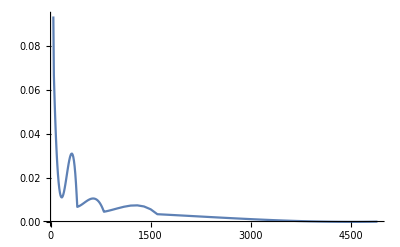

```mathematica
ListPlot[%15,Joined->True]
```

```mathematica
Extrapol
```

InterpolatingFunction[…]

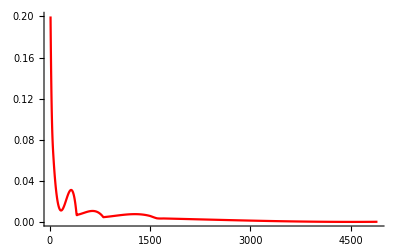

```mathematica
Plot[%226[x],{x,10,4901},PlotRange->All,PlotStyle->Red]
```

```mathematica
Show[%224,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{HoldForm[ζ],None},{HoldForm[z],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True,(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)PlotStyle->{Black,Dashed}]
```

Show::gcomb: Could not combine the graphics objects in Show[{{10,1/5},{50,1/15},{51,29503409/450000000},{52,528881/8203125},{53,3169827/50000000},{54,12271877/196875000},{55,514781/8400000},{56,494212/8203125},«36»,{93,13747763/450000000},{94,1966429/65625000},{95,35267/1200000},{96,1418687/49218750},{97,29682883/1050000000},{98,151621/5468750},«132»},«5»].

Show[{{10,1/5},{50,1/15},{51,29503409/450000000},{52,528881/8203125},{53,3169827/50000000},{54,12271877/196875000},{55,514781/8400000},{56,494212/8203125},{57,26650487/450000000},{58,272873/4687500},{59,60076309/1050000000},{60,3163/56250},{61,58022551/1050000000},{62,1187831/21875000},{63,168067811/3150000000},{64,122863/2343750},{65,61801/1200000},{66,2490107/49218750},{67,7454539/150000000},{68,400424/8203125},{69,151019117/3150000000},{70,24719/525000},{71,2311861/50000000},{72,159619/3515625},{73,46809307/1050000000},{74,205171/4687500},{75,8663/201600},{76,692089/16406250},{77,43479943/1050000000},{78,1143173/28125000},{79,5984167/150000000},{80,1713/43750},{81,17291519/450000000},{82,309326/8203125},{83,38852477/1050000000},{84,893509/24609375},{85,42749/1200000},{86,327673/9375000},{87,108014939/3150000000},{88,39422/1171875},{89,11550233/350000000},{90,25493/787500},{91,33341941/1050000000},{92,73001/2343750},{93,13747763/450000000},{94,1966429/65625000},{95,35267/1200000},{96,1418687/49218750},{97,29682883/1050000000},{98,151621/5468750},{99,12235841/450000000},{100,2/75},{101,27460271/1050000000},{111,67883603/3150000000},{121,2681533/150000000},{131,15814861/1050000000},{141,5865539/450000000},{151,1758703/150000000},{161,3871617/350000000},{171,34572143/3150000000},{181,11964511/1050000000},{191,1837463/150000000},{201,42429713/3150000000},{211,2247643/150000000},{221,2508433/150000000},{231,58637483/3150000000},{241,21619891/1050000000},{251,7902407/350000000},{261,11028779/450000000},{271,27625681/1050000000},{281,4186973/150000000},{291,13161089/450000000},{301,31752871/1050000000},{311,32365801/1050000000},{321,97421993/3150000000},{331,4571923/150000000},{341,10293397/350000000},{351,12441509/450000000},{361,3768493/150000000},{371,22853981/1050000000},{381,55139333/3150000000},{391,12882841/1050000000},{401,24031889/3600000000},{411,512392439/75600000000},{421,8283343/1200000000},{431,25374199/3600000000},{441,545229149/75600000000},{451,62086391/8400000000},{461,63701921/8400000000},{471,84094637/10800000000},{481,67180781/8400000000},{491,29572619/3600000000},{501,91095767/10800000000},{511,72708571/8400000000},{521,223653103/25200000000},{531,687230879/75600000000},{541,11158823/1200000000},{551,79788691/8400000000},{561,104617427/10800000000},{571,11833193/1200000000},{581,252473243/25200000000},{591,767921699/75600000000},{601,86312341/8400000000},{611,37328659/3600000000},{621,789008009/75600000000},{631,12570533/1200000000},{641,4193241/400000000},{651,790558919/75600000000},{661,87318521/8400000000},{671,259419953/25200000000},{681,109650347/10800000000},{691,83728711/8400000000},{701,35051989/3600000000},{711,102138077/10800000000},{721,76666301/8400000000},{731,73444031/8400000000},{741,627779249/75600000000},{751,9367613/1200000000},{761,182650463/25200000000},{771,71566937/10800000000},{781,7127383/1200000000},{791,130645033/25200000000},{801,5382818963/1209600000000},{811,605894417/134400000000},{821,87727561/19200000000},{831,5603956733/1209600000000},{841,90225221/19200000000},{851,274633853/57600000000},{861,5853100703/1209600000000},{871,660148477/134400000000},{881,2010598561/403200000000},{891,874893839/172800000000},{901,690944207/134400000000},{911,33408977/6400000000},{921,915918749/172800000000},{931,723297737/134400000000},{941,2202939941/403200000000},{951,6708629813/1209600000000},{961,108077581/19200000000},{971,2303123731/403200000000},{981,1001408369/172800000000},{991,112859171/19200000000},{1001,801106307/134400000000},{1101,1162170809/172800000000},{1201,139241501/19200000000},{1301,2966337821/403200000000},{1401,1184798909/172800000000},{1501,748216807/134400000000},{1601,11418599467/3427200000000},{1701,1918853453/604800000000},{1801,163805709/54400000000},{1901,1394195681/489600000000},{2001,27582999601/10281600000000},{2101,958516663/380800000000},{2201,383729527/163200000000},{2301,22474030501/10281600000000},{2401,2309240089/1142400000000},{2501,53524793/28800000000},{2601,2493657343/1468800000000},{2701,586330063/380800000000},{2801,4746760667/3427200000000},{2901,1812816043/1468800000000},{3001,414266763/380800000000},{3101,1081416989/1142400000000},{3201,70070279/86400000000},{3301,111238627/163200000000},{3401,112701251/201600000000},{3501,4563554101/10281600000000},{3601,18314309/54400000000},{3701,815771567/3427200000000},{3801,1527285001/10281600000000},{3901,3742409/54400000000},{4001,-34891/54400000000},{4101,-608444099/10281600000000},{4201,-7138783/67200000000},{4301,-69141119/489600000000},{4401,-1681633199/10281600000000},{4501,-65749737/380800000000},{4601,-82228219/489600000000},{4701,-218611757/1468800000000},{4801,-43693037/380800000000},{4901,-4373083/67200000000}},FrameTicks→{{Automatic,None},{Automatic,None}},FrameLabel→{{ζ,None},{z,None}},LabelStyle→{FontFamily→Times New Roman,16,GrayLevel[0]},Frame→True,PlotStyle→{GrayLevel[0],Dashing[{Small,Small}]}]

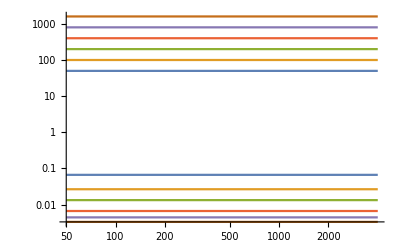

```mathematica
LogLogPlot[l,{x,50,4000}]
```

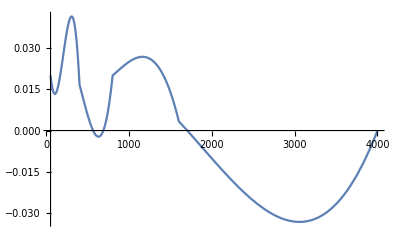

```mathematica
Plot[InterpolatingFunction[{{50,4000}},{5,3,0,{7},{4},0,0,0,0,Automatic,{},{},False},{{50,100,200,400,800,1600,4000}},{{1/50},{1/75},{2/75},{1/60},{1/50},{1/300},{0}},{Automatic}][x],{x,50,4000}]
```

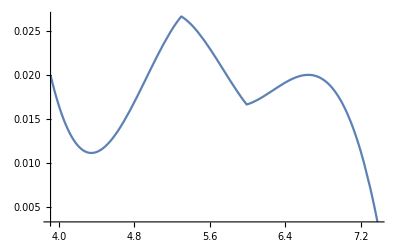

```mathematica
Plot[InterpolatingFunction[{{Log[50],Log[1600]}},{5,3,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{Log[50],Log[100],Log[200],Log[400],Log[800],Log[1600]}},{{1/50},{1/75},{2/75},{1/60},{1/50},{1/300}},{Automatic}][x],{x,Log[50],Log[1600]}]
```

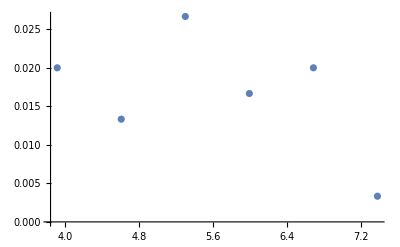

```mathematica
ListPlot[%53]
```

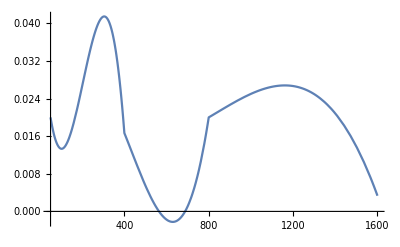

```mathematica
Plot[InterpolatingFunction[{{50,1600}},{5,3,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{50,100,200,400,800,1600}},{{1/50},{1/75},{2/75},{1/60},{1/50},{1/300}},{Automatic}][x],{x,50,1600}]
```

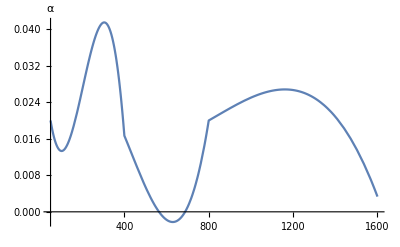

```mathematica
Show[%46,AxesLabel->{None,HoldForm[α]},PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```